```mathematica
Length[list]
Part[list,nth]
Min[list]
IntegerDigits[x,2]
```

```mathematica
Apply[Times,{1,2,3,4,5}]
```

120

```mathematica
not[x_]:=Piecewise[{{0, x==1}, {1, x==0}}]
Map[not,{1,0,1}]
```

```mathematica
Table[Part[{2,3,4},i]^Part[{0,1,0},i],{i,1,3}]
```

```mathematica
Apply[Times,{1,3,1}]
```

3

```mathematica
list:={1,2,3,4,5,6,7,8,9,10}
not[x_]:=Piecewise[{{0, x==1}, {1, x==0}}]
Min[Table[Apply[Times,Table[Part[list,i]^Part[PadLeft[IntegerDigits[x,2],Length[list]],i]+Part[list,i]^Part[PadLeft[Map[not,IntegerDigits[x,2]],Length[list]],i],{i,1,Length[list]}]],{x,1,2^Length[list]-1}]]
Min[Table[Apply[Times,Table[Abs[Part[list,i]^Part[PadLeft[IntegerDigits[x,2],Length[list]],i]-Part[list,i]^Part[PadLeft[Map[not,IntegerDigits[x,2]],Length[list]],i]],{i,1,Length[list]}]],{x,1,2^Length[list]-1}]]
```

5632

0

```mathematica
mm[list_]:=Min[Table[Apply[Times,Table[Part[list,i]^Part[PadLeft[IntegerDigits[x,2],Length[list]],i]+Part[list,i]^Part[PadLeft[Map[not,IntegerDigits[x,2]],Length[list]],i],{i,1,Length[list]}]],{x,1,2^Length[list]-1}]]
```

```mathematica
Monitor[Map[mm,Table[Table[j,{j,1,k}],{k,2,15}]],{k,j,i,x}]
```

{6,16,40,96,224,512,1152,2560,5632,12288,26624,57344,122880,262144}

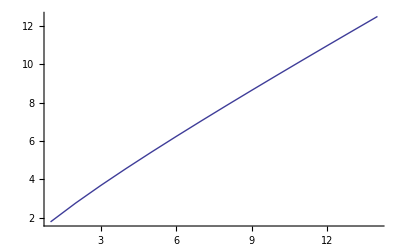

```mathematica
ListPlot[Map[Log,%],Joined->True]
```

```mathematica
Table[x!,{x,2,15}]
```

{2,6,24,120,720,5040,40320,362880,3628800,39916800,479001600,6227020800,87178291200,1307674368000}

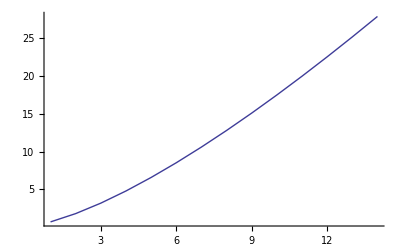

```mathematica
ListPlot[Map[Log,%],Joined->True]
```

{8,24,64,192,448,1152,2560,6144,15360,32768,77824,172032,360448,786432}

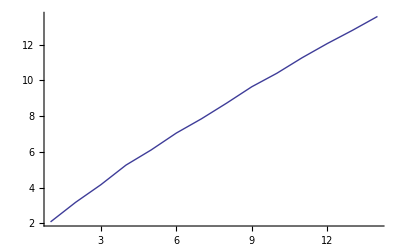

```mathematica
Monitor[Map[mm,Table[Table[Prime[j],{j,1,k}],{k,2,15}]],{k,j,i,x}]
ListPlot[Map[Log,%],Joined->True]
```

{10,40,136,416,1184,3200,8320,20992,51712,124928,296960,696320,1613824,3702784}

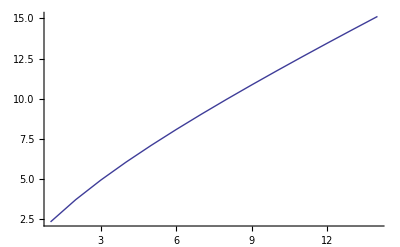

```mathematica
Monitor[Map[mm,Table[Table[j^2,{j,1,k}],{k,2,15}]],{k,j,i,x}]
ListPlot[Map[Log,%],Joined->True]
```

{18,112,520,2016,6944,22016,65664,186880,512512,1363968,3540992,9003008,22487040,55312384}

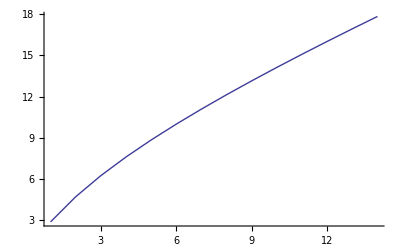

```mathematica
Monitor[Map[mm,Table[Table[j^3,{j,1,k}],{k,2,15}]],{k,j,i,x}]
ListPlot[Map[Log,%],Joined->True]
```

{12,32,80,192,448,1024,2304,5120,11264,24576,53248,114688,245760,524288}

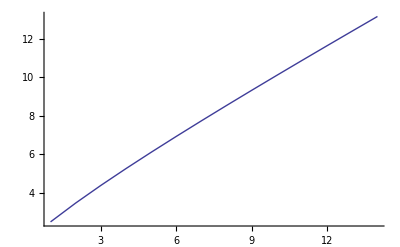

```mathematica
Monitor[Map[mm,Table[Table[2j+1,{j,1,k}],{k,2,15}]],{k,j,i,x}]
ListPlot[Map[Log,%],Joined->True]
```

{10,36,136,528,2080,8256,32896,131328,524800,2098176,8390656,33558528,134225920,536887296}

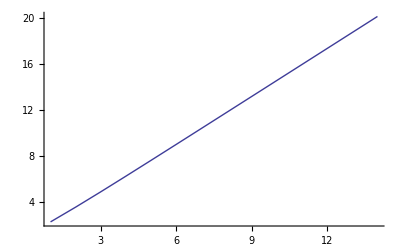

```mathematica
Monitor[Map[mm,Table[Table[2^j,{j,1,k}],{k,2,15}]],{k,j,i,x}]
ListPlot[Map[Log,%],Joined->True]
```

```mathematica
aa:=Map[ad,Partition[RandomInteger[49,50],5]]
aa
Map[mm,aa]
```

{{14,5,7,50,11},{30,28,43,36,12},{2,38,38,36,27},{4,12,2,30,11},{27,23,3,37,29},{41,28,27,46,28},{46,6,17,5,18},{17,3,14,4,45},{41,43,12,15,18},{47,29,19,23,14}}

{656,64,64,736,544,752,720,336,736,784}

```mathematica
ss:=2
dd:=Map[mm,Partition[Flatten[Table[{a,b,c,d,e},{a,1,ss},{b,1,ss},{c,1,ss},{d,1,ss},{e,1,ss}]],5]]
Sort[DeleteDuplicates[dd]]
Length[dd]
Total[dd]/%
```

{32,48}

32

40

```mathematica
ss:=3
dd:=Map[mm,Partition[Flatten[Table[{a,b,c,d,e},{a,1,ss},{b,1,ss},{c,1,ss},{d,1,ss},{e,1,ss}]],5]]
Sort[DeleteDuplicates[dd]]
Length[dd]
Total[dd]/%
```

{32,48,64}

243

48

```mathematica
ss:=4
dd:=Map[mm,Partition[Flatten[Table[{a,b,c,d,e},{a,1,ss},{b,1,ss},{c,1,ss},{d,1,ss},{e,1,ss}]],5]]
Sort[DeleteDuplicates[dd]]
Length[dd]
Total[dd]/%
```

{32,48,64,80}

1024

56

```mathematica
ss:=5
dd:=Map[mm,Partition[Flatten[Table[{a,b,c,d,e},{a,1,ss},{b,1,ss},{c,1,ss},{d,1,ss},{e,1,ss}]],5]]
Sort[DeleteDuplicates[dd]]
Length[dd]
Total[dd]/%
```

{32,48,64,80,96}

3125

64

```mathematica
ss:=6
dd:=Map[mm,Partition[Flatten[Table[{a,b,c,d,e},{a,1,ss},{b,1,ss},{c,1,ss},{d,1,ss},{e,1,ss}]],5]]
Sort[DeleteDuplicates[dd]]
Length[dd]
Total[dd]/%
```

{32,48,64,80,96,112}

7776

72

```mathematica
ss:=7
dd:=Map[mm,Partition[Flatten[Table[{a,b,c,d,e},{a,1,ss},{b,1,ss},{c,1,ss},{d,1,ss},{e,1,ss}]],5]]
Sort[DeleteDuplicates[dd]]
Length[dd]
Total[dd]/%
```

{32,48,64,80,96,112,128}

16807

80

```mathematica
ss:=8
dd:=Map[mm,Partition[Flatten[Table[{a,b,c,d,e},{a,1,ss},{b,1,ss},{c,1,ss},{d,1,ss},{e,1,ss}]],5]]
Sort[DeleteDuplicates[dd]]
Length[dd]
Total[dd]/%
```

{32,48,64,80,96,112,128,144}

32768

88

```mathematica
ss:=9
dd:=Map[mm,Partition[Flatten[Table[{a,b,c,d,e},{a,1,ss},{b,1,ss},{c,1,ss},{d,1,ss},{e,1,ss}]],5]]
Sort[DeleteDuplicates[dd]]
Length[dd]
Total[dd]/%
```

{32,48,64,80,96,112,128,144,160}

59049

96

```mathematica
ss:=10
dd:=Map[mm,Partition[Flatten[Table[{a,b,c,d,e},{a,1,ss},{b,1,ss},{c,1,ss},{d,1,ss},{e,1,ss}]],5]]
Sort[DeleteDuplicates[dd]]
Length[dd]
Total[dd]/%
```

$Aborted

$Aborted

```mathematica
StringSplit["POST POSE ROSE LOSE HOSE HOST MOST MIST MINT LINT LINE LIKE LIFE WIFE 
WINE WINO FINO FINS FIRS FIRE FARE BARE MARE DARE DART DIRT DIRE DIKE 
PIKE POKE POLE PORE SORE SORT FORT FORE MORE CORE BORE TORE TARE TART 
TORT PORT PART CART CARE CASE CAST CANT RANT WANT WANE PANE PANT PAST 
LAST LUST LIST GIST GUST MUST RUST REST BEST TEST ZEST JEST JUST BUST 
DUST FUSE RUSE RISE RITE BITE BITS BATS CATS HATS PATS RATS ROTS BOTS 
BOTH GOTH GOSH POSH NOSH JOSH BOSH COSH CASH RASH SASH LASH BASH GASH 
GASP GAST MAST MASS MARS CARS BARS BANS FANS PANS CANS TANS TINS BINS 
BIND BIRD BARD BARN DARN DARK BARK MARK PARK LARK LARD LORD WORD WORN 
WORE WARE WARD HARD CARD CURD CURE PURE PURL CURL HURL HURT CURT CULT 
CELT WELT FELT MELT PELT BELT BELL TELL YELL HELL FELL FEEL KEEL KEEP 
SEEP PEEP PEER SEER SEED DEED REED READ DEAD BEAD LEAD LEED LEND FEND 
FIND FINE FILE MILE TILE BILE RILE RICE MICE DICE VICE NICE NITE SITE 
SIRE TIRE TINE TINT PINT PINE MINE MIND KIND RIND RING SING DING DINE 
DINK RINK PINK MINK MANX MANE MATE MATH MOTH MOTE MITE MIRE MIKE HIKE 
HIDE TIDE BIDE RIDE RODE ROLE RULE YULE TULE MULE MULL LULL PULL BULL 
HULL CULL DULL SULL NULL FULL GULL GULF GOLD TOLD FOLD MOLD HOLD SOLD 
SOLE HOLE HOPE NOPE ROPE POPE POPS TOPS COPS COWS COWL HOWL FOWL YOWL 
BOWL BOWS BOSS TOSS TOES FOES GOES DOES DOTS POTS PODS PADS CADS DADS 
DAIS DABS DIBS DUBS TUBS CUBS NUBS NUTS BUTS BUTT MUTT MITT MILT LILT 
LILY WILY WILT TILT JILT SILT SALT HALT MALT MALE MALL CALL CALM BALM 
BALE DALE DOLE DOLL POLL TOLL ROLL ROIL FOIL FAIL MAIL TAIL JAIL BAIL 
RAIL HAIL NAIL PAIL SAIL VAIL VAIN PAIN GAIN GAIT WAIT WAIF WAIN WAIL 
WALL BALL BILL TILL SILL SILO SOLO POLO BOLO BOLD COLD WOLD WOLF ROLF 
ROOF ROOM LOOM ZOOM BOOM BOOK TOOK ROOK LOOK LOCK ROCK SOCK MOCK DOCK 
JOCK COCK COCA COCO LOCO LOCH LECH PECH TECH YECH YEAH YEAR FEAR TEAR 
LEAR BEAR HEAR HEAT BEAT BEAN LEAN LEAK TEAK BEAK MEAK MEAL SEAL VEAL 
TEAL REAL DEAL PEAL PEAT MEAT TEAT FEAT NEAT SEAT SEAN JEAN WEAN MEAN 
DEAN DEAR NEAR SEAR PEAR PEAN GEAN YEAN YEAS YENS LENS LENT TENT SENT 
PENT KENT RENT BENT BEND SEND TEND MEND REND PEND POND PONG LONG TONG 
DONG SONG MONG GONG BONG BONE PONE LONE ZONE GONE TONE TUNE DUNE DUNG 
HUNG HUNT BUNT BUNG LUNG LUNA TUNA PUNA PUNE RUNE RUNG SUNG SANG DANG 
DANK DUNK FUNK GUNK GUCK DUCK LUCK RUCK SUCK SUCH MUCH MUCK YUCK TUCK 
BUCK BACK JACK HACK WACK TACK TACO TARO FARO FARL MARL MART KART HART 
WART WARM FARM HARM MARM BARM BERM TERM GERM PERM DERM HERM HELM HOLM 
HOLT COLT BOLT DOLT JOLT MOLT VOLT VOLE TOLE TOKE TOME TOMS TOMB BOMB 
COMB COMP COME CONE COKE CAKE BAKE WAKE FAKE RAKE MAKE HAKE HOKE HOME 
HEME HERE HERD HERO ZERO AERO AERY VERY EERY EELY EELS GELS GELT DELT 
FELT KELT KILT KILL WILL WILD WELD MELD MEAD BEAD BEAU BEAM SEAM TEAM
REAM REAP REAR GEAR WEAR WEAL WEEL TEEL SEEL REEL PEEL PEES PEAS PENS 
PETS BETS BETA FETA FETE FATE PATE PALE SALE TALE GALE GATE GAPE GAZE 
HAZE HALE HALF HALM PALM MALM MAIM MAIN RAIN LAIN LAWN FAWN FAUN FAUX 
FALX FALL PALL GALL HALL HALO CALO CALX CALF CALK TALK WALK BALK BULK 
SULK HULK HUCK HICK PICK LICK LACK LACE FACE MACE RACE RALE RARE HARE 
PARE PARR PARD PARS PARA VARA VARY VARS VATS LATS EATS EATH BATH RATH 
HATH LATH PATH OATH OATS WATS WATT WAST WASP WASH WISH FISH DISH PISH 
PUSH BUSH LUSH TUSH TUSK RUSK BUSK BUSS SUSS WUSS WISS WIST WISP WISE 
WIPE WIRE WIRY AIRY AIRS AIRT AIRN FIRN GIRN KIRN PIRN PORN TORN TURN 
TURK TURF SURF CURF CURD CORD COED TOED TOAD GOAD GOOD WOOD WOOF HOOF 
GOOF GOOP COOP LOOP POOP POOL POOR DOOR DOOM TOOM TOOL
TOOT ROOT FOOT FOOL COOL WOOL MOOL MOOT HOOT BOOT LOOT SOOT SOFT SIFT 
LIFT RIFT GIFT GILT GILL GILD MILD SILD SILK MILK BILK BIRK BISK BISE 
BIZE SIZE SIDE SIPE SIPS TIPS LIPS LAPS LADS LIDS BIDS BADS DADS GADS 
GALS PALS PASS LASS SASS TASS TASK MASK MUSK HUSK DUSK DESK DISK RISK 
RICK SICK TICK NICK DICK MICK WICK KICK KINK KIRK MIRK DIRK DIRL GIRL 
GIRT GIRO GYRO GYRE GORE YORE DORE KORE LORE LORN MORN HORN CORN CORM 
DORM FORM FOAM LOAM LOAF LOAD LOAN MOAN MOON LOON COON GOON POON POOF 
COOF LOOF LOOS MOOS ZOOS BOOS BOOB BLOB BLOC BLOT PLOT PLAT FLAT FLIT 
FRIT BRIT GRIT CRIT CHIT WHIT WHIR WHIZ WHIP CHIP CHOP CHOW CHON CHIN 
THIN SHIN SHIV SPIV SPIT SUIT QUIT QUIP QUIZ QUIN RUIN REIN VEIN ZEIN 
PEIN PEEN SEEN BEEN BEEF BEER LEER JEER JEEP VEEP BEEP BEET WEET FEET 
MEET KEET KEEF REEF REIF REIS LEIS SEIS SEAS TEAS LEAS LEAF LEAP HEAP 
HEAD HEAL ZEAL LEAL FEAL FOAL GOAL GOAT MOAT BOAT DOAT COAT COAX HOAX 
HOAR HOUR TOUR TORR DORR DORY DOXY FOXY BOXY BONY PONY CONY COPY CORY 
COWY GORY TORY LORY LOGY LOGS TOGS TOTS TITS TITI TIKI PIKI PILI HILI 
HILA HULA PULA PUJA PUPA PUPS CUPS TUPS TUTS TATS KATS MATS FATS QATS 
GATS GUTS GUYS BUYS BOYS BOYO TOYO TOYS TONS SONS SINS SINK SUNK LUNK 
PUNK BUNK BANK RANK TANK HANK SANK LANK LANE LAND BAND BOND FOND YOND 
YONI CONI CONS WONS WINS LINS ZINS ZITS PITS PUTS PUTZ PUTT PUNT AUNT 
RUNT LUNT DUNT DENT WENT CENT GENT HENT VENT VEST GEST WEST PEST NEST 
HEST HIST FIST KIST CIST CYST COST LOST TOST WOST WONT WORT WERT VERT 
VEXT SEXT TEXT NEXT NETT NEWT NEWS NETS JETS LETS SETS SETT SECT SEPT 
WEPT KEPT LEPT LEET DEET DUET DUIT DUCT DUCI FUCI FOCI LOCI LOCA SOCA 
SODA SOFA SOLA COLA CODA CODE COLE MOLE JOLE JOKE SOKE MOKE YOKE WOKE 
WOVE WAVE CAVE NAVE RAVE PAVE EAVE GAVE HAVE LAVE LOVE LIVE VIVE RIVE 
FIVE JIVE DIVE GIVE HIVE WIVE WILE PILE PIPE PIPS GIPS GAPS WAPS WAGS 
WARS TARS TAPS TAPA PAPA KAPA KAKA KAKI SAKI SAKE LAKE JAKE TAKE TATE 
SATE HATE LATE DATE BATE CATE RATE RAGE PAGE WAGE CAGE MAGE GAGE GAME 
TAME TIME MIME MOME DOME DOMS MOMS NOMS ROMS RIMS SIMS AIMS VIMS DIMS 
LIMS LIMA LIME LIMP GIMP PIMP PUMP PUMA DUMA DUMB DUMP RUMP RAMP CAMP 
DAMP LAMP LAMB GAMB IAMB JAMB JAMS GAMS HAMS PAMS PAYS PACS PAPS RAPS 
RIPS RIPE YIPE LIPE LIPA LIRA LIRE CIRE CERE SERE DERE WERE FERE FERN 
TERN TEEN THEN THEW WHEW WHEN WHET WHAT CHAT CHAP CRAP TRAP TRAM TRIM 
PRIM PROM PRAM PRAT FRAT FRAP FRAY PRAY TRAY BRAY BRAT BRAG CRAG FRAG 
DRAG DRAT DRAB CRAB CRAM GRAM DRAM DRAW DREW DREG DRUG DRUM DOUM DOUR 
SOUR SOUP SOUL FOUL FOUR YOUR POUR POUT BOUT ROUT TOUT TOFT TOFU TOFF 
TUFF MUFF MIFF BIFF BUFF RUFF RIFF RIFE FIFE FICE LICE BICE BIKE SIKE 
SINE VINE VISE VISA VINA VINO VINY WINY WIND WYND WAND SAND SANE CANE 
CINE BINE BANE JANE FANE FANG TANG BANG GANG HANG HONG HONE DONE DANE 
VANE VANG YANG YANK YACK PACK RACK RECK BECK DECK HECK HOCK NOCK YOCK 
YOLK FOLK FORK WORK WORM NORM NORI TORI TORA TOGA YOGA YUGA RUGA JUGA 
JUGS LUGS LEGS KEGS KEYS KENS KENO LENO LEVO LEVA DEVA DIVA VIVA VIGA 
GIGA GAGA GAGS TAGS BAGS BUGS TUGS HUGS FUGS DUGS DOGS DAGS DIGS FIGS 
RIGS PIGS GIGS JIGS JINS JINK WINK OINK LINK LING PING KING ZING WING 
TING TUNG TUNS PUNS PINS PIÑA MINA MICA PICA PICS PIES TIES TIER PIER 
PIED TIED DIED DIES LIES LIER LIED LIEN LIEU LIEF FIEF KIEF KIER BIER 
BIRR YIRR YIRD YARD FARD SARD NARD NERD NEED FEED WEED TEED TEEM DEEM 
SEEM SEES BEES TEES DEES ZEES ZEDS FEDS BEDS BUDS CUDS PUDS PUSS CUSS 
COSS COSY NOSY ROSY ROPY DOPY DOPE DOVE COVE HOVE ROVE ROBE LOBE LUBE 
TUBE TUBA JUBA JUBE CUBE CUBA SUBA SURA SURE LURE DURE DUKE DUCE PUCE 
PULE PUKE CUKE JUKE JUTE MUTE CUTE LUTE LUNE LUNY PUNY PUNG PANG RANG 
RANI RAND HAND HANT HINT HIND HIED HIES VIES VIEW VIED VIER VEER DEER 
DEEP WEEP WEEK LEEK GEEK GECK NECK PECK FECK KECK KEEK KEEN WEEN WEER 
WEIR HEIR HEIL VEIL DEIL CEIL CELL DELL DELI DEFI DEFT LEFT LEST LESS 
MESS NESS NEBS NIBS NITS NIPS DIPS HIPS HITS KITS WITS WITH KITH KITE 
WITE LITE CITE CETE CEDE REDE REDO REDS PEDS WEDS WETS WEBS DEBS REBS 
RIBS ROBS JOBS COBS COGS BOGS BOGY DOGY FOGY FOGS HOGS JOGS MOGS NOGS 
NAGS NAPS CAPS MAPS MAYS CAYS GAYS DAYS RAYS RAMS CAMS DAMS YAMS BAMS 
LAMS LAME DAME DIME RIME RIMY LIMY LIMO LIDO FIDO FILO KILO KINO KINS 
GINS GUNS NUNS BUNS SUNS SUMS BUMS BUMP HUMP JUMP JIMP WIMP SIMP SUMP 
LUMP TUMP MUMP MUMS HUMS HUTS MUTS RUTS RETS VETS VEES FEES FENS HENS 
HUNS RUNS MUNS MUGS MAGS HAGS HAPS HOPS OOPS BOPS FOPS MOPS MOPE COPE 
LOPE TOPE TOPI TORI TORS DORS DORK CORK CARK NARK NARC NARY WARY WARP 
CARP TARP TARN YARN EARN CARN WARN KARN KERN HERN HERS HERB VERB KERB 
KERF SERF SELF SELL WELL JELL MELL MOLL MILL PILL JILL FILL DILL ZILL 
HILL NILL RILL RIAL VIAL DIAL SIAL PIAL PIAN PLAN PLAY SLAY FLAY CLAY 
CLAM CLAP FLAP FLOP FLIP SLIP SLIT SLUT SLUG PLUG PLUM GLUM SLUM SLIM 
GLIM GLAM SLAM BLAM BLAH BLAB SLAB SLOB SLOW SLOP PLOP PROP DROP TROP 
CROP CROW GROW BROW PROW FROW TROW TROT GROT GROK GOOK COOK COOT CLOT 
SLOT SLAT BLAT BLET BLEW BREW BRED BREE TREE DREE FREE GREE GLEE GLEN 
GLEY FLEY FLEA PLEA PLED BLED SLED FLED GLED GLAD CLAD CLAN CLAW SLAW 
FLAW FLAN FLAX FLAG SLAG SWAG STAG SHAG SNAG SNAP SLAP SOAP SOAR STAR 
STAB STAY SHAY SWAY SWAN SPAN SPAT SPOT SNOT KNOT KNIT SNIT SNIP SKIP 
SKIM SHIM SHAM CHAM WHAM WHIM WHOM WHOA WHOP SHOP SHOT SCOT SCOW SCOP 
STOP STEP STEM STUM SCUM SCUR SCAR SCAM SCAT SCAG SCAB SCAN SCAD SCUD 
SCUP SCUT SMUT SHUT SHUN STUN SPUN SPIN SAIN SAID QAID MAID RAID PAID 
LAID CAID CAIN TAIN FAIN FOIN COIN JOIN LOIN LOWN GOWN DOWN SOWN SOWS 
GOBS SOBS LOBS MOBS NOBS NABS TABS TAMS TAMP VAMP GAMP SAMP SAME NAME 
NAPE CAPE TAPE RAPE RASE RAZE MAZE DAZE LAZE LAZY HAZY MAZY MANY MANE 
GANE KANE KALE VALE WALE WYLE WYTE BYTE BYRE TYRE EYRE LYRE LYSE LOSE 
LOSS MOSS MISS KISS DISS DINS WINS WENS WEND VEND VELD YELD YELP HELP 
HOLP HOLY HOLK HONK BONK ZONK MONK CONK KONK KOOK SOOK NOOK HOOK HOWK 
HAWK HARK SARK WARK WAUK JAUK JOUK SOUK SOUS SODS SOTS COTSCOTE ROTE 
NOTE TOTE VOTE DOTE DOGE DOZE DOSS DOST DUST OUST OAST EAST EASY EASE 
BASE BASS BAYS BAPS BAAS BIAS BRAS ERAS EROS BROS BROO BRIO BRIE BRIG 
PRIG TRIG TRIO TRIP DRIP GRIP GRIG GRIM GRID GRAD GRAN GRIN BRIN BRAN 
BRAD BRAW CRAW CREW GREW GREY GRAY GRUB DRUB DAUB DARB BARB CARB CURB 
BURB BURG BURP BURR PURR CURR CURS BURS OURS FURS FUSS FOSS JOSS JESS 
JEES LEES CEES CUES DUES SUES SUED SHED SNED SPED SPEC SPEW STEW STOW 
SHOW SHOD SHOE SHOO SHOG SNOG SNUG SMUG SMOG SLOG SLOE ALOE ALEE FLEE 
FLEW SLEW SKEW SMEW SHEW CHEW CHEZ CHEF CLEF CLEW PLEW PLOW FLOW GLOW 
GLOB GLIB GLIA ILIA ILKA ILEA OLEA OLEO OLES ODES IDES IRES ARES ORES 
OWES OWLS AWLS AILS AALS BALS BALD BAWD BAWL YAWL PAWL PAWN YAWN MAWN 
MOWN TOWN TOON BOON SOON ZOON NOON NEON PEON PHON PION LION CION COON 
CLON CLOD PLOD PROD PROG FROG FROM FROE FLOE FLUE BLUE BLUR SLUR SLUM 
ALUM ARUM GRUM GRUE TRUE TRUG THUG THUS TAUS TAVS TAWS VAWS PAWS LAWS 
JAWS JARS LARS OARS EARS EARL HARL CARL CAUL WAUL HAUL HAUT TAUT TACT 
FACT PACT PACA CACA CASA VASA VASE PASE PACE PATE PATY PITY CITY MITY 
MIRY MIRS MIBS GIBS FIBS FITS AITS LITS DITS GITS GETS TETS TETH 
METH MESH MOSH MASH DASH FASH HASH HUSH RUSH GUSH MUSH MUSE MISE MISO 
PISO PESO PEPO REPO REPS REGS MEGS BEGS PEGS TEGS SEGS SAGS FAGS ZAGS 
JAGS LAGS RAGS RUGS VUGS VIGS BIGS WIGS ZIGS MIGS MIDS AIDS KIDS GIDS 
FIDS FADS TADS MADS WADS RADS RODS GODS GOOS POOS WOOS COOS CODS BODS 
YODS HODS MODS TODS NODS NODI MODI MODE NODE BODE LODE LOWE HOWE YOWE 
YOWS WOWS MOWS TOWS DOWS LOWS VOWS ROWS HOWS NOWS POWS POLS POLY 
MOLY MOLS MOLA TOLA BOLA KOLA KORA BORA BORN SORN SORA SOYA SOYS JOYS
FOYS COYS HOYS HOLS HOES HOTS HOBS BOBS BIBS SIBS LIBS JIBS JABS WABS"]
```

```mathematica
Length[{"POST","POSE","ROSE","LOSE","HOSE","HOST","MOST","MIST","MINT","LINT","LINE","LIKE","LIFE","WIFE","WINE","WINO","FINO","FINS","FIRS","FIRE","FARE","BARE","MARE","DARE","DART","DIRT","DIRE","DIKE","PIKE","POKE","POLE","PORE","SORE","SORT","FORT","FORE","MORE","CORE","BORE","TORE","TARE","TART","TORT","PORT","PART","CART","CARE","CASE","CAST","CANT","RANT","WANT","WANE","PANE","PANT","PAST","LAST","LUST","LIST","GIST","GUST","MUST","RUST","REST","BEST","TEST","ZEST","JEST","JUST","BUST","DUST","FUSE","RUSE","RISE","RITE","BITE","BITS","BATS","CATS","HATS","PATS","RATS","ROTS","BOTS","BOTH","GOTH","GOSH","POSH","NOSH","JOSH","BOSH","COSH","CASH","RASH","SASH","LASH","BASH","GASH","GASP","GAST","MAST","MASS","MARS","CARS","BARS","BANS","FANS","PANS","CANS","TANS","TINS","BINS","BIND","BIRD","BARD","BARN","DARN","DARK","BARK","MARK","PARK","LARK","LARD","LORD","WORD","WORN","WORE","WARE","WARD","HARD","CARD","CURD","CURE","PURE","PURL","CURL","HURL","HURT","CURT","CULT","CELT","WELT","FELT","MELT","PELT","BELT","BELL","TELL","YELL","HELL","FELL","FEEL","KEEL","KEEP","SEEP","PEEP","PEER","SEER","SEED","DEED","REED","READ","DEAD","BEAD","LEAD","LEED","LEND","FEND","FIND","FINE","FILE","MILE","TILE","BILE","RILE","RICE","MICE","DICE","VICE","NICE","NITE","SITE","SIRE","TIRE","TINE","TINT","PINT","PINE","MINE","MIND","KIND","RIND","RING","SING","DING","DINE","DINK","RINK","PINK","MINK","MANX","MANE","MATE","MATH","MOTH","MOTE","MITE","MIRE","MIKE","HIKE","HIDE","TIDE","BIDE","RIDE","RODE","ROLE","RULE","YULE","TULE","MULE","MULL","LULL","PULL","BULL","HULL","CULL","DULL","SULL","NULL","FULL","GULL","GULF","GOLD","TOLD","FOLD","MOLD","HOLD","SOLD","SOLE","HOLE","HOPE","NOPE","ROPE","POPE","POPS","TOPS","COPS","COWS","COWL","HOWL","FOWL","YOWL","BOWL","BOWS","BOSS","TOSS","TOES","FOES","GOES","DOES","DOTS","POTS","PODS","PADS","CADS","DADS","DAIS","DABS","DIBS","DUBS","TUBS","CUBS","NUBS","NUTS","BUTS","BUTT","MUTT","MITT","MILT","LILT","LILY","WILY","WILT","TILT","JILT","SILT","SALT","HALT","MALT","MALE","MALL","CALL","CALM","BALM","BALE","DALE","DOLE","DOLL","POLL","TOLL","ROLL","ROIL","FOIL","FAIL","MAIL","TAIL","JAIL","BAIL","RAIL","HAIL","NAIL","PAIL","SAIL","VAIL","VAIN","PAIN","GAIN","GAIT","WAIT","WAIF","WAIN","WAIL","WALL","BALL","BILL","TILL","SILL","SILO","SOLO","POLO","BOLO","BOLD","COLD","WOLD","WOLF","ROLF","ROOF","ROOM","LOOM","ZOOM","BOOM","BOOK","TOOK","ROOK","LOOK","LOCK","ROCK","SOCK","MOCK","DOCK","JOCK","COCK","COCA","COCO","LOCO","LOCH","LECH","PECH","TECH","YECH","YEAH","YEAR","FEAR","TEAR","LEAR","BEAR","HEAR","HEAT","BEAT","BEAN","LEAN","LEAK","TEAK","BEAK","MEAK","MEAL","SEAL","VEAL","TEAL","REAL","DEAL","PEAL","PEAT","MEAT","TEAT","FEAT","NEAT","SEAT","SEAN","JEAN","WEAN","MEAN","DEAN","DEAR","NEAR","SEAR","PEAR","PEAN","GEAN","YEAN","YEAS","YENS","LENS","LENT","TENT","SENT","PENT","KENT","RENT","BENT","BEND","SEND","TEND","MEND","REND","PEND","POND","PONG","LONG","TONG","DONG","SONG","MONG","GONG","BONG","BONE","PONE","LONE","ZONE","GONE","TONE","TUNE","DUNE","DUNG","HUNG","HUNT","BUNT","BUNG","LUNG","LUNA","TUNA","PUNA","PUNE","RUNE","RUNG","SUNG","SANG","DANG","DANK","DUNK","FUNK","GUNK","GUCK","DUCK","LUCK","RUCK","SUCK","SUCH","MUCH","MUCK","YUCK","TUCK","BUCK","BACK","JACK","HACK","WACK","TACK","TACO","TARO","FARO","FARL","MARL","MART","KART","HART","WART","WARM","FARM","HARM","MARM","BARM","BERM","TERM","GERM","PERM","DERM","HERM","HELM","HOLM","HOLT","COLT","BOLT","DOLT","JOLT","MOLT","VOLT","VOLE","TOLE","TOKE","TOME","TOMS","TOMB","BOMB","COMB","COMP","COME","CONE","COKE","CAKE","BAKE","WAKE","FAKE","RAKE","MAKE","HAKE","HOKE","HOME","HEME","HERE","HERD","HERO","ZERO","AERO","AERY","VERY","EERY","EELY","EELS","GELS","GELT","DELT","FELT","KELT","KILT","KILL","WILL","WILD","WELD","MELD","MEAD","BEAD","BEAU","BEAM","SEAM","TEAM","REAM","REAP","REAR","GEAR","WEAR","WEAL","WEEL","TEEL","SEEL","REEL","PEEL","PEES","PEAS","PENS","PETS","BETS","BETA","FETA","FETE","FATE","PATE","PALE","SALE","TALE","GALE","GATE","GAPE","GAZE","HAZE","HALE","HALF","HALM","PALM","MALM","MAIM","MAIN","RAIN","LAIN","LAWN","FAWN","FAUN","FAUX","FALX","FALL","PALL","GALL","HALL","HALO","CALO","CALX","CALF","CALK","TALK","WALK","BALK","BULK","SULK","HULK","HUCK","HICK","PICK","LICK","LACK","LACE","FACE","MACE","RACE","RALE","RARE","HARE","PARE","PARR","PARD","PARS","PARA","VARA","VARY","VARS","VATS","LATS","EATS","EATH","BATH","RATH","HATH","LATH","PATH","OATH","OATS","WATS","WATT","WAST","WASP","WASH","WISH","FISH","DISH","PISH","PUSH","BUSH","LUSH","TUSH","TUSK","RUSK","BUSK","BUSS","SUSS","WUSS","WISS","WIST","WISP","WISE","WIPE","WIRE","WIRY","AIRY","AIRS","AIRT","AIRN","FIRN","GIRN","KIRN","PIRN","PORN","TORN","TURN","TURK","TURF","SURF","CURF","CURD","CORD","COED","TOED","TOAD","GOAD","GOOD","WOOD","WOOF","HOOF","GOOF","GOOP","COOP","LOOP","POOP","POOL","POOR","DOOR","DOOM","TOOM","TOOL","TOOT","ROOT","FOOT","FOOL","COOL","WOOL","MOOL","MOOT","HOOT","BOOT","LOOT","SOOT","SOFT","SIFT","LIFT","RIFT","GIFT","GILT","GILL","GILD","MILD","SILD","SILK","MILK","BILK","BIRK","BISK","BISE","BIZE","SIZE","SIDE","SIPE","SIPS","TIPS","LIPS","LAPS","LADS","LIDS","BIDS","BADS","DADS","GADS","GALS","PALS","PASS","LASS","SASS","TASS","TASK","MASK","MUSK","HUSK","DUSK","DESK","DISK","RISK","RICK","SICK","TICK","NICK","DICK","MICK","WICK","KICK","KINK","KIRK","MIRK","DIRK","DIRL","GIRL","GIRT","GIRO","GYRO","GYRE","GORE","YORE","DORE","KORE","LORE","LORN","MORN","HORN","CORN","CORM","DORM","FORM","FOAM","LOAM","LOAF","LOAD","LOAN","MOAN","MOON","LOON","COON","GOON","POON","POOF","COOF","LOOF","LOOS","MOOS","ZOOS","BOOS","BOOB","BLOB","BLOC","BLOT","PLOT","PLAT","FLAT","FLIT","FRIT","BRIT","GRIT","CRIT","CHIT","WHIT","WHIR","WHIZ","WHIP","CHIP","CHOP","CHOW","CHON","CHIN","THIN","SHIN","SHIV","SPIV","SPIT","SUIT","QUIT","QUIP","QUIZ","QUIN","RUIN","REIN","VEIN","ZEIN","PEIN","PEEN","SEEN","BEEN","BEEF","BEER","LEER","JEER","JEEP","VEEP","BEEP","BEET","WEET","FEET","MEET","KEET","KEEF","REEF","REIF","REIS","LEIS","SEIS","SEAS","TEAS","LEAS","LEAF","LEAP","HEAP","HEAD","HEAL","ZEAL","LEAL","FEAL","FOAL","GOAL","GOAT","MOAT","BOAT","DOAT","COAT","COAX","HOAX","HOAR","HOUR","TOUR","TORR","DORR","DORY","DOXY","FOXY","BOXY","BONY","PONY","CONY","COPY","CORY","COWY","GORY","TORY","LORY","LOGY","LOGS","TOGS","TOTS","TITS","TITI","TIKI","PIKI","PILI","HILI","HILA","HULA","PULA","PUJA","PUPA","PUPS","CUPS","TUPS","TUTS","TATS","KATS","MATS","FATS","QATS","GATS","GUTS","GUYS","BUYS","BOYS","BOYO","TOYO","TOYS","TONS","SONS","SINS","SINK","SUNK","LUNK","PUNK","BUNK","BANK","RANK","TANK","HANK","SANK","LANK","LANE","LAND","BAND","BOND","FOND","YOND","YONI","CONI","CONS","WONS","WINS","LINS","ZINS","ZITS","PITS","PUTS","PUTZ","PUTT","PUNT","AUNT","RUNT","LUNT","DUNT","DENT","WENT","CENT","GENT","HENT","VENT","VEST","GEST","WEST","PEST","NEST","HEST","HIST","FIST","KIST","CIST","CYST","COST","LOST","TOST","WOST","WONT","WORT","WERT","VERT","VEXT","SEXT","TEXT","NEXT","NETT","NEWT","NEWS","NETS","JETS","LETS","SETS","SETT","SECT","SEPT","WEPT","KEPT","LEPT","LEET","DEET","DUET","DUIT","DUCT","DUCI","FUCI","FOCI","LOCI","LOCA","SOCA","SODA","SOFA","SOLA","COLA","CODA","CODE","COLE","MOLE","JOLE","JOKE","SOKE","MOKE","YOKE","WOKE","WOVE","WAVE","CAVE","NAVE","RAVE","PAVE","EAVE","GAVE","HAVE","LAVE","LOVE","LIVE","VIVE","RIVE","FIVE","JIVE","DIVE","GIVE","HIVE","WIVE","WILE","PILE","PIPE","PIPS","GIPS","GAPS","WAPS","WAGS","WARS","TARS","TAPS","TAPA","PAPA","KAPA","KAKA","KAKI","SAKI","SAKE","LAKE","JAKE","TAKE","TATE","SATE","HATE","LATE","DATE","BATE","CATE","RATE","RAGE","PAGE","WAGE","CAGE","MAGE","GAGE","GAME","TAME","TIME","MIME","MOME","DOME","DOMS","MOMS","NOMS","ROMS","RIMS","SIMS","AIMS","VIMS","DIMS","LIMS","LIMA","LIME","LIMP","GIMP","PIMP","PUMP","PUMA","DUMA","DUMB","DUMP","RUMP","RAMP","CAMP","DAMP","LAMP","LAMB","GAMB","IAMB","JAMB","JAMS","GAMS","HAMS","PAMS","PAYS","PACS","PAPS","RAPS","RIPS","RIPE","YIPE","LIPE","LIPA","LIRA","LIRE","CIRE","CERE","SERE","DERE","WERE","FERE","FERN","TERN","TEEN","THEN","THEW","WHEW","WHEN","WHET","WHAT","CHAT","CHAP","CRAP","TRAP","TRAM","TRIM","PRIM","PROM","PRAM","PRAT","FRAT","FRAP","FRAY","PRAY","TRAY","BRAY","BRAT","BRAG","CRAG","FRAG","DRAG","DRAT","DRAB","CRAB","CRAM","GRAM","DRAM","DRAW","DREW","DREG","DRUG","DRUM","DOUM","DOUR","SOUR","SOUP","SOUL","FOUL","FOUR","YOUR","POUR","POUT","BOUT","ROUT","TOUT","TOFT","TOFU","TOFF","TUFF","MUFF","MIFF","BIFF","BUFF","RUFF","RIFF","RIFE","FIFE","FICE","LICE","BICE","BIKE","SIKE","SINE","VINE","VISE","VISA","VINA","VINO","VINY","WINY","WIND","WYND","WAND","SAND","SANE","CANE","CINE","BINE","BANE","JANE","FANE","FANG","TANG","BANG","GANG","HANG","HONG","HONE","DONE","DANE","VANE","VANG","YANG","YANK","YACK","PACK","RACK","RECK","BECK","DECK","HECK","HOCK","NOCK","YOCK","YOLK","FOLK","FORK","WORK","WORM","NORM","NORI","TORI","TORA","TOGA","YOGA","YUGA","RUGA","JUGA","JUGS","LUGS","LEGS","KEGS","KEYS","KENS","KENO","LENO","LEVO","LEVA","DEVA","DIVA","VIVA","VIGA","GIGA","GAGA","GAGS","TAGS","BAGS","BUGS","TUGS","HUGS","FUGS","DUGS","DOGS","DAGS","DIGS","FIGS","RIGS","PIGS","GIGS","JIGS","JINS","JINK","WINK","OINK","LINK","LING","PING","KING","ZING","WING","TING","TUNG","TUNS","PUNS","PINS","PIÑA","MINA","MICA","PICA","PICS","PIES","TIES","TIER","PIER","PIED","TIED","DIED","DIES","LIES","LIER","LIED","LIEN","LIEU","LIEF","FIEF","KIEF","KIER","BIER","BIRR","YIRR","YIRD","YARD","FARD","SARD","NARD","NERD","NEED","FEED","WEED","TEED","TEEM","DEEM","SEEM","SEES","BEES","TEES","DEES","ZEES","ZEDS","FEDS","BEDS","BUDS","CUDS","PUDS","PUSS","CUSS","COSS","COSY","NOSY","ROSY","ROPY","DOPY","DOPE","DOVE","COVE","HOVE","ROVE","ROBE","LOBE","LUBE","TUBE","TUBA","JUBA","JUBE","CUBE","CUBA","SUBA","SURA","SURE","LURE","DURE","DUKE","DUCE","PUCE","PULE","PUKE","CUKE","JUKE","JUTE","MUTE","CUTE","LUTE","LUNE","LUNY","PUNY","PUNG","PANG","RANG","RANI","RAND","HAND","HANT","HINT","HIND","HIED","HIES","VIES","VIEW","VIED","VIER","VEER","DEER","DEEP","WEEP","WEEK","LEEK","GEEK","GECK","NECK","PECK","FECK","KECK","KEEK","KEEN","WEEN","WEER","WEIR","HEIR","HEIL","VEIL","DEIL","CEIL","CELL","DELL","DELI","DEFI","DEFT","LEFT","LEST","LESS","MESS","NESS","NEBS","NIBS","NITS","NIPS","DIPS","HIPS","HITS","KITS","WITS","WITH","KITH","KITE","WITE","LITE","CITE","CETE","CEDE","REDE","REDO","REDS","PEDS","WEDS","WETS","WEBS","DEBS","REBS","RIBS","ROBS","JOBS","COBS","COGS","BOGS","BOGY","DOGY","FOGY","FOGS","HOGS","JOGS","MOGS","NOGS","NAGS","NAPS","CAPS","MAPS","MAYS","CAYS","GAYS","DAYS","RAYS","RAMS","CAMS","DAMS","YAMS","BAMS","LAMS","LAME","DAME","DIME","RIME","RIMY","LIMY","LIMO","LIDO","FIDO","FILO","KILO","KINO","KINS","GINS","GUNS","NUNS","BUNS","SUNS","SUMS","BUMS","BUMP","HUMP","JUMP","JIMP","WIMP","SIMP","SUMP","LUMP","TUMP","MUMP","MUMS","HUMS","HUTS","MUTS","RUTS","RETS","VETS","VEES","FEES","FENS","HENS","HUNS","RUNS","MUNS","MUGS","MAGS","HAGS","HAPS","HOPS","OOPS","BOPS","FOPS","MOPS","MOPE","COPE","LOPE","TOPE","TOPI","TORI","TORS","DORS","DORK","CORK","CARK","NARK","NARC","NARY","WARY","WARP","CARP","TARP","TARN","YARN","EARN","CARN","WARN","KARN","KERN","HERN","HERS","HERB","VERB","KERB","KERF","SERF","SELF","SELL","WELL","JELL","MELL","MOLL","MILL","PILL","JILL","FILL","DILL","ZILL","HILL","NILL","RILL","RIAL","VIAL","DIAL","SIAL","PIAL","PIAN","PLAN","PLAY","SLAY","FLAY","CLAY","CLAM","CLAP","FLAP","FLOP","FLIP","SLIP","SLIT","SLUT","SLUG","PLUG","PLUM","GLUM","SLUM","SLIM","GLIM","GLAM","SLAM","BLAM","BLAH","BLAB","SLAB","SLOB","SLOW","SLOP","PLOP","PROP","DROP","TROP","CROP","CROW","GROW","BROW","PROW","FROW","TROW","TROT","GROT","GROK","GOOK","COOK","COOT","CLOT","SLOT","SLAT","BLAT","BLET","BLEW","BREW","BRED","BREE","TREE","DREE","FREE","GREE","GLEE","GLEN","GLEY","FLEY","FLEA","PLEA","PLED","BLED","SLED","FLED","GLED","GLAD","CLAD","CLAN","CLAW","SLAW","FLAW","FLAN","FLAX","FLAG","SLAG","SWAG","STAG","SHAG","SNAG","SNAP","SLAP","SOAP","SOAR","STAR","STAB","STAY","SHAY","SWAY","SWAN","SPAN","SPAT","SPOT","SNOT","KNOT","KNIT","SNIT","SNIP","SKIP","SKIM","SHIM","SHAM","CHAM","WHAM","WHIM","WHOM","WHOA","WHOP","SHOP","SHOT","SCOT","SCOW","SCOP","STOP","STEP","STEM","STUM","SCUM","SCUR","SCAR","SCAM","SCAT","SCAG","SCAB","SCAN","SCAD","SCUD","SCUP","SCUT","SMUT","SHUT","SHUN","STUN","SPUN","SPIN","SAIN","SAID","QAID","MAID","RAID","PAID","LAID","CAID","CAIN","TAIN","FAIN","FOIN","COIN","JOIN","LOIN","LOWN","GOWN","DOWN","SOWN","SOWS","GOBS","SOBS","LOBS","MOBS","NOBS","NABS","TABS","TAMS","TAMP","VAMP","GAMP","SAMP","SAME","NAME","NAPE","CAPE","TAPE","RAPE","RASE","RAZE","MAZE","DAZE","LAZE","LAZY","HAZY","MAZY","MANY","MANE","GANE","KANE","KALE","VALE","WALE","WYLE","WYTE","BYTE","BYRE","TYRE","EYRE","LYRE","LYSE","LOSE","LOSS","MOSS","MISS","KISS","DISS","DINS","WINS","WENS","WEND","VEND","VELD","YELD","YELP","HELP","HOLP","HOLY","HOLK","HONK","BONK","ZONK","MONK","CONK","KONK","KOOK","SOOK","NOOK","HOOK","HOWK","HAWK","HARK","SARK","WARK","WAUK","JAUK","JOUK","SOUK","SOUS","SODS","SOTS","COTSCOTE","ROTE","NOTE","TOTE","VOTE","DOTE","DOGE","DOZE","DOSS","DOST","DUST","OUST","OAST","EAST","EASY","EASE","BASE","BASS","BAYS","BAPS","BAAS","BIAS","BRAS","ERAS","EROS","BROS","BROO","BRIO","BRIE","BRIG","PRIG","TRIG","TRIO","TRIP","DRIP","GRIP","GRIG","GRIM","GRID","GRAD","GRAN","GRIN","BRIN","BRAN","BRAD","BRAW","CRAW","CREW","GREW","GREY","GRAY","GRUB","DRUB","DAUB","DARB","BARB","CARB","CURB","BURB","BURG","BURP","BURR","PURR","CURR","CURS","BURS","OURS","FURS","FUSS","FOSS","JOSS","JESS","JEES","LEES","CEES","CUES","DUES","SUES","SUED","SHED","SNED","SPED","SPEC","SPEW","STEW","STOW","SHOW","SHOD","SHOE","SHOO","SHOG","SNOG","SNUG","SMUG","SMOG","SLOG","SLOE","ALOE","ALEE","FLEE","FLEW","SLEW","SKEW","SMEW","SHEW","CHEW","CHEZ","CHEF","CLEF","CLEW","PLEW","PLOW","FLOW","GLOW","GLOB","GLIB","GLIA","ILIA","ILKA","ILEA","OLEA","OLEO","OLES","ODES","IDES","IRES","ARES","ORES","OWES","OWLS","AWLS","AILS","AALS","BALS","BALD","BAWD","BAWL","YAWL","PAWL","PAWN","YAWN","MAWN","MOWN","TOWN","TOON","BOON","SOON","ZOON","NOON","NEON","PEON","PHON","PION","LION","CION","COON","CLON","CLOD","PLOD","PROD","PROG","FROG","FROM","FROE","FLOE","FLUE","BLUE","BLUR","SLUR","SLUM","ALUM","ARUM","GRUM","GRUE","TRUE","TRUG","THUG","THUS","TAUS","TAVS","TAWS","VAWS","PAWS","LAWS","JAWS","JARS","LARS","OARS","EARS","EARL","HARL","CARL","CAUL","WAUL","HAUL","HAUT","TAUT","TACT","FACT","PACT","PACA","CACA","CASA","VASA","VASE","PASE","PACE","PATE","PATY","PITY","CITY","MITY","MIRY","MIRS","MIBS","GIBS","FIBS","FITS","AITS","LITS","DITS","GITS","GETS","TETS","TETH","METH","MESH","MOSH","MASH","DASH","FASH","HASH","HUSH","RUSH","GUSH","MUSH","MUSE","MISE","MISO","PISO","PESO","PEPO","REPO","REPS","REGS","MEGS","BEGS","PEGS","TEGS","SEGS","SAGS","FAGS","ZAGS","JAGS","LAGS","RAGS","RUGS","VUGS","VIGS","BIGS","WIGS","ZIGS","MIGS","MIDS","AIDS","KIDS","GIDS","FIDS","FADS","TADS","MADS","WADS","RADS","RODS","GODS","GOOS","POOS","WOOS","COOS","CODS","BODS","YODS","HODS","MODS","TODS","NODS","NODI","MODI","MODE","NODE","BODE","LODE","LOWE","HOWE","YOWE","YOWS","WOWS","MOWS","TOWS","DOWS","LOWS","VOWS","ROWS","HOWS","NOWS","POWS","POLS","POLY","MOLY","MOLS","MOLA","TOLA","BOLA","KOLA","KORA","BORA","BORN","SORN","SORA","SOYA","SOYS","JOYS","FOYS","COYS","HOYS","HOLS","HOES","HOTS","HOBS","BOBS","BIBS","SIBS","LIBS","JIBS","JABS","WABS"}]
```

2192

```mathematica
StringReplace[%,{"A"->"2","B"->"2","C"->"2","D"->"3","E"->"3","F"->"3","G"->"4","H"->"4","I"->"4","J"->"5","K"->"5","L"->"5","M"->"6","N"->"6","O"->"6","P"->"7","Q"->"7","R"->"7","S"->"7","T"->"8","U"->"8","V"->"8","W"->"9","Z"->"9","Y"->"9","Z"->"9"}]
```

```mathematica
ww:={"7678","7673","7673","5673","4673","4678","6678","6478","6468","5468","5463","5453","5433","9433","9463","9466","3466","3467","3477","3473","3273","2273","6273","3273","3278","3478","3473","3453","7453","7653","7653","7673","7673","7678","3678","3673","6673","2673","2673","8673","8273","8278","8678","7678","7278","2278","2273","2273","2278","2268","7268","9268","9263","7263","7268","7278","5278","5878","5478","4478","4878","6878","7878","7378","2378","8378","9378","5378","5878","2878","3878","3873","7873","7473","7483","2483","2487","2287","2287","4287","7287","7287","7687","2687","2684","4684","4674","7674","6674","5674","2674","2674","2274","7274","7274","5274","2274","4274","4277","4278","6278","6277","6277","2277","2277","2267","3267","7267","2267","8267","8467","2467","2463","2473","2273","2276","3276","3275","2275","6275","7275","5275","5273","5673","9673","9676","9673","9273","9273","4273","2273","2873","2873","7873","7875","2875","4875","4878","2878","2858","2358","9358","3358","6358","7358","2358","2355","8355","9355","4355","3355","3335","5335","5337","7337","7337","7337","7337","7333","3333","7333","7323","3323","2323","5323","5333","5363","3363","3463","3463","3453","6453","8453","2453","7453","7423","6423","3423","8423","6423","6483","7483","7473","8473","8463","8468","7468","7463","6463","6463","5463","7463","7464","7464","3464","3463","3465","7465","7465","6465","626X","6263","6283","6284","6684","6683","6483","6473","6453","4453","4433","8433","2433","7433","7633","7653","7853","9853","8853","6853","6855","5855","7855","2855","4855","2855","3855","7855","6855","3855","4855","4853","4653","8653","3653","6653","4653","7653","7653","4653","4673","6673","7673","7673","7677","8677","2677","2697","2695","4695","3695","9695","2695","2697","2677","8677","8637","3637","4637","3637","3687","7687","7637","7237","2237","3237","3247","3227","3427","3827","8827","2827","6827","6887","2887","2888","6888","6488","6458","5458","5459","9459","9458","8458","5458","7458","7258","4258","6258","6253","6255","2255","2256","2256","2253","3253","3653","3655","7655","8655","7655","7645","3645","3245","6245","8245","5245","2245","7245","4245","6245","7245","7245","8245","8246","7246","4246","4248","9248","9243","9246","9245","9255","2255","2455","8455","7455","7456","7656","7656","2656","2653","2653","9653","9653","7653","7663","7666","5666","9666","2666","2665","8665","7665","5665","5625","7625","7625","6625","3625","5625","2625","2622","2626","5626","5624","5324","7324","8324","9324","9324","9327","3327","8327","5327","2327","4327","4328","2328","2326","5326","5325","8325","2325","6325","6325","7325","8325","8325","7325","3325","7325","7328","6328","8328","3328","6328","7328","7326","5326","9326","6326","3326","3327","6327","7327","7327","7326","4326","9326","9327","9367","5367","5368","8368","7368","7368","5368","7368","2368","2363","7363","8363","6363","7363","7363","7663","7664","5664","8664","3664","7664","6664","4664","2664","2663","7663","5663","9663","4663","8663","8863","3863","3864","4864","4868","2868","2864","5864","5862","8862","7862","7863","7863","7864","7864","7264","3264","3265","3865","3865","4865","4825","3825","5825","7825","7825","7824","6824","6825","9825","8825","2825","2225","5225","4225","9225","8225","8226","8276","3276","3275","6275","6278","5278","4278","9278","9276","3276","4276","6276","2276","2376","8376","4376","7376","3376","4376","4356","4656","4658","2658","2658","3658","5658","6658","8658","8653","8653","8653","8663","8667","8662","2662","2662","2667","2663","2663","2653","2253","2253","9253","3253","7253","6253","4253","4653","4663","4363","4373","4373","4376","9376","2376","2379","8379","3379","3359","3357","4357","4358","3358","3358","5358","5458","5455","9455","9453","9353","6353","6323","2323","2328","2326","7326","8326","7326","7327","7327","4327","9327","9325","9335","8335","7335","7335","7335","7337","7327","7367","7387","2387","2382","3382","3383","3283","7283","7253","7253","8253","4253","4283","4273","4293","4293","4253","4253","4256","7256","6256","6246","6246","7246","5246","5296","3296","3286","328X","325X","3255","7255","4255","4255","4256","2256","225X","2253","2255","8255","9255","2255","2855","7855","4855","4825","4425","7425","5425","5225","5223","3223","6223","7223","7253","7273","4273","7273","7277","7273","7277","7272","8272","8279","8277","8287","5287","3287","3284","2284","7284","4284","5284","7284","6284","6287","9287","9288","9278","9277","9274","9474","3474","3474","7474","7874","2874","5874","8874","8875","7875","2875","2877","7877","9877","9477","9478","9477","9473","9473","9473","9479","2479","2477","2478","2476","3476","4476","5476","7476","7676","8676","8876","8875","8873","7873","2873","2873","2673","2633","8633","8623","4623","4663","9663","9663","4663","4663","4667","2667","5667","7667","7665","7667","3667","3666","8666","8665","8668","7668","3668","3665","2665","9665","6665","6668","4668","2668","5668","7668","7638","7438","5438","7438","4438","4458","4455","4453","6453","7453","7455","6455","2455","2475","2475","2473","2493","7493","7433","7473","7477","8477","5477","5277","5237","5437","2437","2237","3237","4237","4257","7257","7277","5277","7277","8277","8275","6275","6875","4875","3875","3375","3475","7475","7425","7425","8425","6425","3425","6425","9425","5425","5465","5475","6475","3475","3475","4475","4478","4476","4976","4973","4673","9673","3673","5673","5673","5676","6676","4676","2676","2676","3676","3676","3626","5626","5623","5623","5626","6626","6666","5666","2666","4666","7666","7663","2663","5663","5667","6667","9667","2667","2662","2562","2562","2568","7568","7528","3528","3548","3748","2748","4748","2748","2448","9448","9447","9449","9447","2447","2467","2469","2466","2446","8446","7446","7448","7748","7748","7848","7848","7847","7849","7846","7846","7346","8346","9346","7346","7336","7336","2336","2333","2337","5337","5337","5337","8337","2337","2338","9338","3338","6338","5338","5333","7333","7343","7347","5347","7347","7327","8327","5327","5323","5327","4327","4323","4325","9325","5325","3325","3625","4625","4628","6628","2628","3628","2628","262X","462X","4627","4687","8687","8677","3677","3679","36X9","36X9","26X9","2669","7669","2669","2679","2679","2699","4679","8679","5679","5649","5647","8647","8687","8487","8484","8454","7454","7454","4454","4452","4852","7852","7852","7872","7877","2877","8877","8887","8287","5287","6287","3287","7287","4287","4887","4897","2897","2697","2696","8696","8697","8667","7667","7467","7465","7865","5865","7865","2865","2265","7265","8265","4265","7265","5265","5263","5263","2263","2663","3663","9663","9664","2664","2667","9667","9467","5467","9467","9487","7487","7887","7889","7888","7868","2868","7868","5868","3868","3368","9368","2368","4368","4368","8368","8378","4378","9378","7378","6378","4378","4478","3478","5478","2478","2978","2678","5678","8678","9678","9668","9678","9378","8378","83X8","73X8","83X8","63X8","6388","6398","6397","6387","5387","5387","7387","7388","7328","7378","9378","5378","5378","5338","3338","3838","3848","3828","3824","3824","3624","5624","5622","7622","7632","7632","7652","2652","2632","2633","2653","6653","5653","5653","7653","6653","9653","9653","9683","9283","2283","6283","7283","7283","3283","4283","4283","5283","5683","5483","8483","7483","3483","5483","3483","4483","4483","9483","9453","7453","7473","7477","4477","4277","9277","9247","9277","8277","8277","8272","7272","5272","5252","5254","7254","7253","5253","5253","8253","8283","7283","4283","5283","3283","2283","2283","7283","7243","7243","9243","2243","6243","4243","4263","8263","8463","6463","6663","3663","3667","6667","6667","7667","7467","7467","2467","8467","3467","5467","5462","5463","5467","4467","7467","7867","7862","3862","3862","3867","7867","7267","2267","3267","5267","5262","4262","4262","5262","5267","4267","4267","7267","7297","7227","7277","7277","7477","7473","9473","5473","5472","5472","5473","2473","2373","7373","3373","9373","3373","3376","8376","8336","8436","8439","9439","9436","9438","9428","2428","2427","2727","8727","8726","8746","7746","7766","7726","7728","3728","3727","3729","7729","8729","2729","2728","2724","2724","3724","3724","3728","3722","2722","2726","4726","3726","3729","3739","3734","3784","3786","3686","3687","7687","7687","7685","3685","3687","9687","7687","7688","2688","7688","8688","8638","8638","8633","8833","6833","6433","2433","2833","7833","7433","7433","3433","3423","5423","2423","2453","7453","7463","8463","8473","8472","8462","8466","8469","9469","9463","9963","9263","7263","7263","2263","2463","2463","2263","5263","3263","3264","8264","2264","4264","4264","4664","4663","3663","3263","8263","8264","9264","9265","9225","7225","7225","7325","2325","3325","4325","4625","6625","9625","9655","3655","3675","9675","9676","6676","6674","8674","8672","8642","9642","9842","7842","5842","5847","5847","5347","5347","5397","5367","5366","5366","5386","5382","3382","3482","8482","8442","4442","4242","4247","8247","2247","2847","8847","4847","3847","3847","3647","3247","3447","3447","7447","7447","4447","5447","5467","5465","9465","6465","5465","5464","7464","5464","9464","9464","8464","8864","8867","7867","7467","74Ñ2","6462","6422","7422","7427","7437","8437","8437","7437","7433","8433","3433","3437","5437","5437","5433","5436","5438","5433","3433","5433","5437","2437","2477","9477","9473","9273","3273","7273","6273","6373","6333","3333","9333","8333","8336","3336","7336","7337","2337","8337","3337","9337","9337","3337","2337","2837","2837","7837","7877","2877","2677","2679","6679","7679","7679","3679","3673","3683","2683","4683","7683","7623","5623","5823","8823","8822","5822","5823","2823","2822","7822","7872","7873","5873","3873","3853","3823","7823","7853","7853","2853","5853","5883","6883","2883","5883","5863","5869","7869","7864","7264","7264","7264","7263","4263","4268","4468","4463","4433","4437","8437","8439","8433","8437","8337","3337","3337","9337","9335","5335","4335","4325","6325","7325","3325","5325","5335","5336","9336","9337","9347","4347","4345","8345","3345","2345","2355","3355","3354","3334","3338","5338","5378","5377","6377","6377","6327","6427","6487","6477","3477","4477","4487","5487","9487","9484","5484","5483","9483","5483","2483","2383","2333","7333","7336","7337","7337","9337","9387","9327","3327","7327","7427","7627","5627","2627","2647","2647","2649","3649","3649","3647","4647","5647","6647","6647","6247","6277","2277","6277","6297","2297","4297","3297","7297","7267","2267","3267","9267","2267","5267","5263","3263","3463","7463","7469","5469","5466","5436","3436","3456","5456","5466","5467","4467","4867","6867","2867","7867","7867","2867","2867","4867","5867","5467","9467","7467","7867","5867","8867","6867","6867","4867","4887","6887","7887","7387","8387","8337","3337","3367","4367","4867","7867","6867","6847","6247","4247","4277","4677","6677","2677","3677","6677","6673","2673","5673","8673","8674","8674","8677","3677","3675","2675","2275","6275","6272","6279","9279","9277","2277","8277","8276","9276","3276","2276","9276","5276","5376","4376","4377","4372","8372","5372","5373","7373","7353","7355","9355","5355","6355","6655","6455","7455","5455","3455","3455","9455","4455","6455","7455","7425","8425","3425","7425","7425","7426","7526","7529","7529","3529","2529","2526","2527","3527","3567","3547","7547","7548","7588","7584","7584","7586","4586","7586","7546","4546","4526","7526","2526","2524","2522","7522","7562","7569","7567","7567","7767","3767","8767","2767","2769","4769","2769","7769","3769","8769","8768","4768","4765","4665","2665","2668","2568","7568","7528","2528","2538","2539","2739","2733","2733","8733","3733","3733","4733","4533","4536","4539","3539","3532","7532","7533","2533","7533","3533","4533","4523","2523","2526","2529","7529","3529","3526","352X","3524","7524","7924","7824","7424","7624","7627","7527","7627","7627","7827","7822","7829","7429","7929","7926","7726","7728","7768","7668","5668","5648","7648","7647","7547","7546","7446","7426","2426","9426","9446","9466","9462","9467","7467","7468","7268","7269","7267","7867","7837","7836","7886","7286","7287","7227","7226","7228","7224","7222","7226","7223","7283","7287","7288","7688","7488","7486","7886","7786","7746","7246","7243","7243","6243","7243","7243","5243","2243","2246","8246","3246","3646","2646","5646","5646","5696","4696","3696","7696","7697","4627","7627","5627","6627","6627","6227","8227","8267","8267","8267","4267","7267","7263","6263","6273","2273","8273","7273","7273","7293","6293","3293","5293","5299","4299","6299","6269","6263","4263","5263","5253","8253","9253","9953","9983","2983","2973","8973","3973","5973","5973","5673","5677","6677","6477","5477","3477","3467","9467","9367","9363","8363","8353","9353","9357","4357","4657","4659","4655","4665","2665","9665","6665","2665","5665","5665","7665","6665","4665","4695","4295","4275","7275","9275","9285","5285","5685","7685","7687","7637","7687","26872683","7683","6683","8683","8683","3683","3643","3693","3677","3678","3878","6878","6278","3278","3279","3273","2273","2277","2297","2277","2227","2427","2727","3727","3767","2767","2766","2746","2743","2744","7744","8744","8746","8747","3747","4747","4744","4746","4743","4723","4726","4746","2746","2726","2723","2729","2729","2739","4739","4739","4729","4782","3782","3282","3272","2272","2272","2872","2872","2874","2877","2877","7877","2877","2877","2877","6877","3877","3877","3677","5677","5377","5337","5337","2337","2837","3837","7837","7833","7433","7633","7733","7732","7739","7839","7869","7469","7463","7463","7466","7464","7664","7684","7684","7664","7564","7563","2563","2533","3533","3539","7539","7539","7639","7439","2439","2439","2433","2533","2539","7539","7569","3569","4569","4562","4542","4542","4542","4552","4532","6532","6536","6537","6337","4337","4737","2737","6737","6937","6957","2957","2457","2257","2257","2253","2293","2295","9295","7295","7296","9296","6296","6696","8696","8666","2666","7666","9666","6666","6366","7366","7466","7466","5466","2466","2666","2566","2563","7563","7763","7764","3764","3766","3763","3563","3583","2583","2587","7587","7586","2586","2786","4786","4783","8783","8784","8484","8487","8287","8287","8297","8297","7297","5297","5297","5277","5277","6277","3277","3275","4275","2275","2285","9285","4285","4288","8288","8228","3228","7228","7222","2222","2272","8272","8273","7273","7223","7283","7289","7489","2489","6489","6479","6477","6427","4427","3427","3487","2487","5487","3487","4487","4387","8387","8384","6384","6374","6674","6274","3274","3274","4274","4874","7874","4874","6874","6873","6473","6476","7476","7376","7376","7376","7377","7347","6347","2347","7347","8347","7347","7247","3247","9247","5247","5247","7247","7847","8847","8447","2447","9447","9447","6447","6437","2437","5437","4437","3437","3237","8237","6237","9237","7237","7637","4637","4667","7667","9667","2667","2637","2637","9637","4637","6637","8637","6637","6634","6634","6633","6633","2633","5633","5693","4693","9693","9697","9697","6697","8697","3697","5697","8697","7697","4697","6697","7697","7657","7659","6659","6657","6652","8652","2652","5652","5672","2672","2676","7676","7672","7692","7697","5697","3697","2697","4697","4657","4637","4687","4627","2627","2427","7427","5427","5427","5227","9227"}
```

```mathematica
Length[ww]
Length[DeleteDuplicates[ww]]
```

2192

1240

```mathematica
Clear[list]
```

```mathematica
Map[ToString,{aahs,abay,abba,abbe,abbr,abed,abet,abib,abid,abit,able,ably,abox,abra,abut,abye,acct,aced,aces,ache,achy,acid,aclu,acme,acne,acre,acts,acyl,adam,adar,adaw,adds,adit,ados,adry,advt,adze,aeon,aero,aery,afar,afer,affy,afro,agar,aged,agen,ages,agha,agin,agio,agni,agog,agon,agre,ague,ahem,ahey,ahoy,aide,aids,aiel,ails,aims,aino,airs,airy,ajar,ajog,akin,alae,alai,alan,alar,alas,alba,albe,albs,alco,alee,alem,ales,alew,alfa,alga,alii,alit,alls,ally,alma,alme,alms,aloe,alow,alps,also,alto,alum,amah,ambo,amel,amen,amex,amia,amic,amid,amir,amis,amit,amma,ammo,amok,amps,amts,amyl,anal,anan,anas,ands,anes,anet,anew,anil,anis,ankh,anna,anne,anno,anoa,anon,ansa,ansi,anta,ante,anti,ants,anus,apar,aped,aper,apes,apex,apis,apod,apse,apus,aqua,arab,arak,arch,arco,arcs,area,ares,aret,arew,argo,aria,arid,aril,arks,arms,army,arna,arow,arse,arts,arty,arum,asap,asci,asea,ashy,asia,asks,asps,asse,assn,asst,atma,atmo,atom,atop,atte,attn,atty,atwo,aube,auks,auld,auln,aune,aunt,aura,auto,avdp,avel,aver,aves,avid,avie,avis,avow,away,awed,awes,awls,awns,awny,awol,awry,axal,axed,axel,axes,axil,axis,axle,axon,ayah,ayen,ayes,ayle,ayme,ayry,azym,baal,baas,baba,babe,babu,baby,bace,bach,back,bade,bads,baff,baft,bags,baht,bail,bain,bait,bake,bald,bale,bali,balk,ball,balm,banc,band,bane,bang,bank,bans,barb,bard,bare,barf,bark,barm,barn,bars,base,bash,bask,bass,bast,bate,bath,bats,batz,baud,bauk,bawd,bawl,bawn,baya,bays,bdrm,bead,beak,beal,beam,bean,bear,beat,beau,beck,bede,beds,beef,beem,been,beep,beer,bees,beet,bega,begs,behn,belk,bell,belt,bema,bend,bene,bens,bent,bere,berg,berm,bess,best,beta,bete,bets,bevy,beys,bias,bibb,bibs,bice,bide,bids,bier,biff,biga,bigg,bike,bikh,bile,bilk,bill,bind,bine,bing,bink,bins,biol,bion,bios,bird,birk,birl,birr,birt,bise,bish,bisk,bite,bito,bits,bitt,blab,blae,blah,blat,blay,bldg,blea,bleb,bled,blee,blek,blet,blew,blin,blip,blob,bloc,blot,blow,blub,blue,blur,blvd,boar,boas,boat,bobs,boca,boce,bock,bode,bods,body,boer,boes,boff,bogs,bogy,boil,boke,bola,bold,bole,boll,boln,bolo,bolt,bomb,bona,bond,bone,bong,bono,bons,bony,boob,book,boom,boon,boor,boos,boot,bops,bord,bore,born,bort,bosa,bosh,bosk,boss,bote,both,bots,boud,bouk,boul,boun,bour,bout,bowl,bows,boxy,boyo,boys,boza,bozo,brad,brae,brag,bran,bras,brat,braw,bray,bred,bren,bret,brew,brid,brie,brig,brim,brin,brio,brit,brob,brog,bros,brow,bruh,brun,brut,buat,bubo,bubs,buck,buds,buff,bufo,bugs,buhl,bulb,bulk,bull,bump,bums,bund,bung,bunk,bunn,buns,bunt,buoy,burg,burh,burl,burn,burp,burr,burs,burt,bury,bush,busk,buss,bust,busy,buts,butt,buys,buzz,byes,byre,byss,byte,caas,cabs,cack,cade,cadi,cads,cady,cafe,cage,cagy,cake,caky,calc,calf,cali,calk,call,calm,calx,came,camp,cams,cand,cane,cans,cant,cany,cape,caps,card,care,carf,cark,carl,carp,cars,cart,casa,case,cash,cask,cass,cast,cata,cate,cats,cauf,cauk,caul,cave,cavy,cawk,caws,cayo,cays,ceca,cede,cees,ceil,cell,celt,cent,cere,cero,cert,cess,cest,cete,chab,chad,chak,cham,chap,char,chat,chaw,chef,chem,ches,chew,chez,chia,chic,chid,chin,chip,chit,chop,chou,chow,chub,chud,chug,chum,ciao,cill,cima,cine,cion,circ,cist,cite,city,cive,cize,clad,clam,clan,clap,claw,clay,clee,clef,cleg,clem,clew,clio,clip,clod,clog,clop,clot,cloy,club,clue,clum,cmdg,coag,coak,coal,coat,coax,cobs,coca,cock,coco,coda,code,cods,coed,cogs,coho,coif,coil,coin,coir,coit,coke,cola,cold,cole,coll,colp,colt,coly,coma,comb,come,comp,cond,cone,conf,cong,conj,conk,conn,cons,cont,cony,cook,cool,coom,coon,coop,coos,coot,cope,cops,copy,cora,corb,cord,core,corf,cork,corm,corn,corp,cosh,coss,cost,cosy,cote,cots,coup,cove,cowl,cows,coxa,cozy,crab,crag,cram,cran,crap,craw,cray,cree,crew,crib,cric,crop,crow,crud,crup,crus,crut,crux,ctrl,cuba,cube,cubs,cuca,cuds,cued,cues,cuff,cuke,cull,culm,cult,cund,cunt,cups,curb,curd,cure,curl,curr,curs,curt,cusk,cusp,cuss,cute,cuts,cyan,cyma,cyme,cyon,cyst,czar,dabb,dabs,dace,dada,dade,dado,dads,daff,daft,dago,dais,dale,dalf,dame,damn,damp,dams,dana,dane,dang,dank,dare,darg,dark,darn,darr,dart,dase,dash,data,date,daub,dauk,daun,dauw,dave,dawe,dawk,dawn,days,daze,dbms,dead,deaf,deal,dean,dear,deas,debs,debt,deck,deco,dede,deed,deem,deep,deer,dees,deev,deft,defy,degu,deil,deis,deja,dele,delf,deli,dell,deme,demi,demo,demy,dens,dent,deny,dept,dere,derf,derk,derm,dern,desk,dess,deus,deux,deva,deve,devi,dews,dewy,deye,deys,dhow,diag,dial,diam,dian,dias,dibs,dice,dich,dick,dict,dido,didy,died,diem,dies,diet,digs,dika,dike,dill,dime,dims,dine,ding,dink,dins,dint,dips,dipt,dire,dirk,dirl,dirt,disc,dish,disk,dite,ditt,diva,dive,dizz,djin,doab,doat,dock,docs,dodd,dodo,doer,does,doff,doge,dogs,dogy,doit,dojo,doko,dole,dolf,doll,dolt,dome,doms,dona,done,dong,doni,dons,doom,doop,door,dope,dopy,dorm,dorn,dorp,dorr,dors,dory,dose,doss,dost,dote,doth,dots,doty,douc,dour,dout,dove,dowl,down,dows,doxy,doze,dozy,drab,drad,drag,dram,drat,draw,dray,dree,dreg,drek,drew,drey,drib,drie,drip,droh,drop,drow,drub,drug,drum,drys,duad,dual,duan,dubb,dubs,duce,duck,duct,dude,duds,duel,dues,duet,duff,dugs,duke,dull,duly,dumb,dump,dune,dung,dunk,duns,dunt,duos,dupe,dura,dure,durn,duse,dusk,dust,duty,dyad,dyas,dyed,dyer,dyes,dyke,dyne,each,eale,eame,earl,earn,ears,ease,east,easy,eath,eats,eaux,eave,ebbs,ebon,eccl,eche,echo,ecol,econ,ecru,ecus,edam,edda,eddy,eden,edge,edgy,edit,eeke,eels,eely,eery,effs,efts,egad,egal,eger,eggs,egis,egos,egre,eigh,eild,eire,ejoo,eked,ekes,elan,elds,elhi,elix,elke,elks,ells,elms,elmy,else,elul,elve,emeu,emew,emir,emit,emmy,emus,emyd,encl,ends,engr,enow,envy,eons,epee,epen,epha,epic,epos,eras,erat,ergo,ergs,eric,erie,erin,erke,erme,erne,erns,eros,errs,erse,ersh,erst,eses,esox,espy,esse,etch,ethe,etna,etui,etym,euge,eugh,eval,even,ever,eves,evet,evil,ewer,ewes,ewry,exam,exec,exes,exit,exon,expo,eyas,eyed,eyen,eyer,eyes,eyet,eyle,eyne,eyot,eyra,eyre,eyry,face,fact,fade,fads,fady,fags,fail,fain,fair,fait,fake,falk,fall,falx,fame,fand,fane,fang,fans,fard,fare,farl,farm,faro,fart,fash,fast,fate,fats,faun,faut,faux,fawe,fawn,fays,faze,feal,fear,feat,feck,feds,feed,feel,fees,feet,fehm,fele,fell,felt,feme,fend,fens,feod,fere,ferm,fern,fers,fess,fest,feta,fete,feud,fiar,fiat,fibs,fica,fice,fico,fide,fido,fids,fief,fife,figs,fiji,fike,file,fill,film,fils,find,fine,fink,finn,fins,fint,fire,firk,firm,firs,fisc,fish,fisk,fist,fits,fitt,fitz,five,fixe,fizz,flab,flag,flak,flam,flan,flap,flat,flaw,flax,flay,flea,fled,flee,flet,flew,flex,flip,flit,flix,floe,flog,flon,flop,flow,flub,flue,flus,flux,foal,foam,fobs,foci,foes,foge,fogs,fogy,foil,foin,fold,folk,fond,fone,font,food,fool,foot,fops,fora,ford,fore,fork,form,fort,foul,four,fowl,foxy,fozy,frab,frag,frap,frat,frau,fray,fred,free,fren,fret,frig,frim,frit,friz,froe,frog,from,frow,frug,fuar,fubs,fuci,fuck,fuds,fuel,fuff,fuga,fugh,fugs,fuji,full,fume,fumy,fund,funk,furl,furs,fury,fuse,fuss,fust,fuze,fuzz,fyke,fyrd,gabs,gaby,gade,gads,gael,gaff,gaga,gage,gags,gain,gait,gala,gale,gall,gals,galt,game,gamp,gams,gamy,gane,gang,gaol,gape,gaps,gapy,garb,gard,gare,gars,gary,gash,gasp,gast,gate,gats,gaud,gaul,gaur,gave,gawk,gawn,gays,gaze,geal,gean,gear,geat,geck,gedd,geed,geek,geer,gees,geet,geez,geic,gein,geld,gels,gelt,gems,gena,gene,gens,gent,genu,geog,geol,geom,gere,germ,gern,gery,gest,geth,gets,geum,ghat,ghee,gibe,gibs,gide,gift,gigs,gila,gild,gile,gill,gilt,gimp,ging,ginn,gins,gips,gird,gire,girl,girn,girt,gise,gist,gite,gith,give,glad,glee,gleg,glen,glew,gley,glib,glim,glob,glom,glop,glow,glue,glum,glut,glyn,gnar,gnat,gnaw,gnew,gnof,gnow,gnus,goad,goaf,goal,goar,goat,gobs,goby,gode,gods,goel,goen,goer,goes,goff,gogo,gold,golf,goll,gome,gone,gong,good,goof,gook,goon,goop,goos,goot,gord,gore,gorm,gory,gosh,goss,gote,goth,goud,gour,gout,gove,govt,gowd,gowk,gowl,gown,goys,grab,grad,graf,gram,gras,gray,gree,gres,gret,grew,grey,grid,grig,gril,grim,grin,grip,gris,grit,grog,gros,grot,grow,grub,gruf,grum,guam,guan,guar,guck,guff,guhr,guib,guid,gula,gule,gulf,gull,gulp,gult,guly,gump,gums,guna,gung,gunk,guns,gurl,gurt,guru,gush,gust,guts,guys,guze,gybe,gyle,gyms,gyps,gyre,gyri,gyro,gyse,gyte,gyve,haaf,haak,haar,hack,hade,hadj,haft,hags,hahs,haik,hail,hair,haji,hajj,hake,hale,half,halk,hall,halm,halo,halp,hals,halt,hame,hams,hand,hang,hank,haps,hard,hare,hark,harl,harm,harp,hart,hary,hase,hash,hask,hasp,hast,hate,hath,hats,haul,haum,haut,have,hawk,hawm,haws,haye,hays,haze,hazy,head,heal,heam,heap,hear,heat,hebe,heck,heed,heel,heep,heer,heft,heil,heir,held,hele,hell,helm,help,heme,hemp,hems,heng,hens,hent,herb,herd,here,herl,hern,hero,herr,hers,hert,hery,hesp,hest,hete,heuk,hewe,hewn,hews,hexa,heyh,hick,hide,hied,hies,high,hike,hile,hill,hilt,hind,hine,hink,hint,hipe,hips,hire,hirs,hisn,hiss,hist,hits,hive,hizz,hoar,hoax,hobo,hobs,hock,hods,hoed,hoer,hoes,hogh,hogo,hogs,hoit,hoke,hold,hole,holm,holp,holt,holy,home,homo,homy,hond,hone,hong,honk,hont,hood,hoof,hook,hool,hoom,hoop,hoot,hope,hopi,hops,hora,hore,horn,hors,hose,hosp,host,hote,hots,houp,hour,hove,howe,howl,howp,hows,hubs,huch,huck,hued,huer,hues,huff,huge,hugs,hugy,huke,hula,hulk,hull,hump,hums,hung,hunk,huns,hunt,hurl,hurr,hurt,hush,husk,huso,huts,huzz,hyde,hyen,hyke,hymn,hyne,hype,hypo,iamb,ibex,ibid,ibis,icbm,iced,ices,icky,icon,idea,idee,idem,ideo,ides,idle,idly,idol,idyl,ieee,iffy,ihvh,ikon,ilex,ilia,ilke,ilks,ills,illy,imam,iman,impi,imps,inca,ince,inch,inde,inee,info,inia,inks,inky,inly,inne,inns,inro,inst,intl,into,intr,ions,iota,iowa,ipso,iran,iraq,ired,ires,iris,irks,iron,irpe,isis,isle,isms,ital,itch,item,iter,iuds,iwis,ixia,izar,jabs,jack,jade,jagg,jags,jail,jain,jake,jako,jamb,jams,jane,jant,jape,jarl,jars,jasp,jato,java,jawn,jaws,jawy,jays,jazz,jean,jeat,jeel,jeep,jeer,jeez,jefe,jehu,jell,jerk,jess,jest,jesu,jets,jeux,jews,jibb,jibe,jibs,jiff,jigs,jill,jilt,jimp,jink,jinn,jins,jinx,jive,jobs,jock,joes,joey,jogs,john,joie,join,joke,jole,joll,jolt,jose,josh,joso,joss,jota,jots,jouk,joul,jour,jove,jowl,joys,juan,juba,jube,judo,judy,juga,juge,jugs,juju,juke,juli,july,jump,june,junk,juno,jupe,jura,jure,jury,just,jute,juts,kadi,kage,kagu,kail,kain,kaka,kale,kali,kama,kame,kami,kand,karn,kart,kate,kava,kawn,kayo,kays,keck,keel,keen,keep,kegs,keir,keld,kele,kell,kelp,kelt,kemb,kemp,keno,kens,kent,kepi,kept,kerb,kerf,kerl,kern,kers,kess,kest,keta,keys,khan,kibe,kiby,kick,kids,kier,kiev,kike,kill,kiln,kilo,kilt,kind,kine,king,kink,kino,kins,kipe,kips,kirk,kish,kiss,kist,kite,kith,kits,kiva,kive,kiwi,knab,knag,knap,knar,knaw,knee,knew,knit,knob,knop,knor,knot,know,knox,knur,koan,koba,koel,koff,kohl,kola,kong,kook,koto,kris,ksar,kuda,kudo,kudu,kung,kurd,kwhr,kyar,kyat,kyaw,kyke,laas,labs,lace,lack,lacy,lade,lads,lady,laft,lags,laic,laid,lain,lair,lait,lake,lakh,laky,lalo,lama,lamb,lame,lamm,lamp,lams,land,lane,lang,lank,lant,laos,lapp,laps,lard,lare,lark,lars,lary,lash,lask,lass,last,lata,late,lath,laud,laus,lava,lave,lawe,lawm,lawn,laws,lays,laze,lazy,lead,leaf,leak,leal,leam,lean,leap,lear,leas,leat,lech,lect,leed,leef,leek,leep,leer,lees,leet,left,lege,legs,leis,leks,leme,lena,lend,lene,leno,lens,lent,leod,leon,leos,lere,lese,less,lest,lete,lets,leva,leve,levi,levo,levy,lewd,leys,liar,lias,libs,lice,lich,lick,lido,lids,lied,lief,lien,lier,lies,lieu,life,lift,lige,like,lill,lilt,lily,lima,limb,lime,limn,limo,limp,limu,limy,lind,line,ling,link,lino,lins,lint,liny,lion,lips,lira,lire,lisp,liss,list,lite,lith,lits,live,lixt,liza,load,loaf,loam,loan,lobe,lobo,lobs,loca,loch,loci,lock,loco,lode,loft,loge,logo,logs,logy,loin,loir,loke,loki,loll,loma,lond,lone,long,loob,loof,look,lool,loom,loon,loop,loos,loot,lope,lops,lord,lore,lori,lorn,lory,lose,loss,lost,lote,loth,loto,lots,loud,louk,loup,lour,lout,love,lowh,lowk,lown,lows,luau,lube,luce,luck,lucy,lues,luff,luge,lugs,luke,lull,lulu,lump,luna,lune,lung,lunk,lunt,luny,lure,lurg,lurk,lush,lusk,lust,lute,luth,luxe,lyam,lyes,lyne,lynx,lyra,lyre,maad,maat,mace,mach,mack,macs,made,mads,mage,magi,mags,maha,maia,maid,mail,maim,main,make,maki,mala,male,mali,mall,malm,malt,mama,mand,mane,mano,mans,manu,manx,many,maps,mara,marc,mare,mark,marl,mars,mart,marx,mary,mase,mash,mask,mass,mast,mate,math,mats,matt,maty,maud,maul,maut,mawk,maws,maxi,maya,mayo,mays,maze,mazy,mead,meak,meal,mean,mear,meas,meat,meaw,mech,mede,meed,meek,meer,meet,mega,mein,meld,mell,melt,memo,mend,mens,ment,menu,meow,merd,mere,merk,merl,mero,mesa,mesh,mess,mest,meta,mete,meth,meum,meve,mewl,mews,mias,mibs,mica,mice,mich,mick,mico,mida,midi,mids,mien,miff,migo,migs,mike,mild,mile,milk,mill,mils,milt,mime,mina,mind,mine,ming,mini,mink,mins,mint,minx,miny,mira,mire,mirk,mirv,miry,misc,mise,miso,miss,mist,misy,mite,mitt,mitu,mity,mixt,mktg,moan,moas,moat,mobs,mock,moco,mode,modi,modo,mods,mody,moff,moha,moho,mohr,moil,moke,moky,mola,mold,mole,moll,molt,moly,mome,moms,mona,mone,monk,mono,mons,mont,mony,mood,moon,moor,moos,moot,mope,mops,mopy,mora,more,morn,moro,mort,mosk,moss,most,mote,moth,moto,mots,moue,moun,move,mowe,mown,mows,moxa,moya,msec,muce,much,muck,muds,muff,mugs,mule,mull,mumm,mump,mums,mund,mung,muon,mure,murk,murr,musa,muse,mush,musk,muss,must,mute,mutt,muxy,myna,myth,myxa,nabk,nabs,nags,naid,naif,naik,nail,nais,nake,nale,nall,name,namo,naos,nape,naps,napu,narc,nard,nare,nark,nart,nary,nasa,nash,nath,natl,nato,naut,nave,navy,nawl,nays,nayt,naze,nazi,neaf,neal,neap,near,neat,nebs,neck,need,neer,neif,nems,neon,nepa,nerd,nere,nero,nese,nesh,ness,nest,nets,neve,nevi,news,newt,next,nias,nibs,nice,nick,nide,nief,nigh,nile,nill,nils,nilt,nims,nine,nips,nipt,nisi,nits,nixy,noah,nobs,nock,node,nods,noel,noes,nogs,noie,noil,noir,nole,noll,nolo,nolt,noma,nome,noms,none,nook,noon,noot,nope,norm,norn,nose,nosh,nost,nosy,nota,note,nots,nott,noun,nous,nova,novo,nowd,nows,nowt,nubs,nude,nuke,null,numb,nuns,nurl,nuts,nyas,oafs,oaks,oaky,oars,oary,oast,oath,oats,obbe,obey,obis,obit,oboe,obol,ocra,odal,odds,odes,odic,odin,odor,odyl,ofay,offs,ogam,ogee,ogle,ogre,ohed,ohio,ohms,oils,oily,oink,oint,okay,oker,okie,okra,olay,olds,olea,oleo,oles,olid,olio,olla,olpe,omen,omer,omit,once,onde,ones,only,onto,onus,onyx,oohs,oops,ooze,oozy,opah,opal,opec,open,opes,opie,opts,opus,opye,oral,orbs,orby,orca,orch,orcs,ordo,ores,orfe,orgy,orig,orle,orlo,orth,orts,oryx,osar,oslo,ossa,osse,otic,otis,otto,ouch,ours,ouse,oust,outs,ouze,ouzo,oval,oven,over,ovid,ovum,owch,owed,owel,owen,owes,owls,owns,owre,owse,oxen,oxes,oxid,oyer,oyes,oyez,paas,paca,pace,pack,paco,pacs,pact,pacu,pads,page,pahi,paid,pail,pain,pair,pais,pale,pali,pall,palm,palo,palp,pals,paly,pane,pang,pans,pant,papa,pape,paps,para,pard,pare,park,parr,pars,part,pash,pask,paso,pass,past,pate,path,pats,paul,paum,pave,pavo,pawk,pawl,pawn,paws,payn,pays,peag,peak,peal,pean,pear,peas,peat,peba,peck,peds,peed,peek,peel,peen,peep,peer,pees,pegm,pegs,pein,peke,pela,pelf,pell,pelt,pend,penk,pens,pent,peon,pepo,peps,pere,peri,perk,perm,pern,pers,pert,peru,pery,pese,peso,pest,pets,pews,phew,phiz,phys,phyz,pial,pian,pica,pice,pici,pick,pics,pied,pier,pies,piet,pigg,pigs,pika,pike,pile,pill,pily,pima,pimp,pina,pine,ping,pink,pins,pint,piny,pion,piot,pipa,pipe,pips,pipy,pirl,pirn,pisa,pise,pish,piss,pist,pita,pith,pits,pity,pius,pixy,pkwy,plan,plat,play,plea,pled,pley,plim,ploc,plod,plop,plot,plow,ploy,plug,plum,plus,pnyx,poak,pock,poco,pods,poem,poet,pogy,poke,poky,pole,polk,poll,polo,pols,polt,poly,pome,pomp,pond,pone,pong,pons,pony,pood,pooh,pool,poon,poop,poor,pope,pops,pore,pork,porn,port,pory,pose,posh,poss,post,posy,pots,pott,pouf,poup,pour,pout,powp,pows,poze,prad,pram,prat,pray,prep,pres,prey,prie,prig,prim,pris,prix,proa,proc,prod,prof,prog,prom,pron,prop,pros,prow,prox,psst,pubs,puce,puck,puds,pudu,pued,puer,puet,puff,pugh,pugs,puit,puke,pule,pull,pulp,pult,pulu,puma,pume,pump,pumy,puna,pung,punk,puns,punt,puny,puoy,pupa,pupe,pups,pure,puri,purl,purr,push,puss,puts,putt,pyet,pyin,pyla,pyne,pyot,pyre,pyro,qaid,qoph,quab,quad,quae,quag,quai,qual,quam,quap,quar,quas,quat,quay,quem,ques,quet,quey,quia,quib,quid,quin,quip,quit,quiz,quob,quod,quop,quos,raca,race,rach,rack,racy,rade,rads,raff,raft,raga,rage,rags,raia,raid,rail,rain,raip,rais,raja,rake,raki,rale,rami,ramp,rams,rana,rand,rang,rani,rank,rant,rape,raps,rapt,rara,rare,rase,rash,rasp,rata,rate,rath,rats,rave,raws,rays,raze,razz,rcpt,read,reak,real,ream,reap,rear,rebs,recd,reck,recs,rede,redo,reds,reed,reef,reek,reel,reem,refs,reft,reif,reim,rein,reis,reit,rely,reme,rems,rend,reng,reno,rent,reps,rese,resp,rest,retd,rete,reve,revs,rewe,reyn,rhea,rhob,rhus,rial,ribs,rice,rich,rick,ride,rids,rief,riel,rife,riff,rift,rigs,rile,rill,rily,rima,rime,rims,rimy,rind,rine,ring,rink,riot,ripe,rips,rise,rish,risk,rist,rite,ritz,rive,road,roam,roan,roar,robe,robs,rock,rocs,rode,rods,rody,roed,roes,roil,roin,roke,roky,role,roll,rome,romp,roms,rong,ront,rood,roof,rook,room,roon,roop,root,rope,ropy,rory,rosa,rose,ross,rost,rosy,rota,rote,roto,rots,roty,roue,rouk,roun,roup,rout,roux,rove,rown,rows,rube,rubs,ruby,ruck,rudd,rude,rued,ruer,rues,ruff,ruft,ruga,rugs,ruin,rukh,rule,ruly,rump,rums,rune,rung,runs,runt,ruse,rush,rusk,russ,rust,ruth,ruts,ryal,ryas,ryes,rynd,ryot,rysh,ryth,saan,sack,sacs,sadh,sadr,safe,saga,sage,sago,sags,sagy,saic,said,sail,saim,sain,sake,saki,sale,salm,salp,salt,same,samp,sand,sane,sang,sank,sans,saps,sard,sari,sark,sarn,sart,sash,sass,sate,sauf,sauh,saul,saur,saut,save,sawn,saws,says,scab,scad,scag,scam,scan,scar,scat,scil,scop,scot,scow,scry,scud,scug,scum,scup,scur,scut,scye,sdan,seah,seak,seal,seam,sean,sear,seas,seat,seck,secs,sect,seed,seek,seel,seem,seen,seep,seer,sees,seet,sego,seid,seke,seld,self,sell,sely,seme,semi,send,sens,sent,sept,sera,serb,sere,serf,serr,sess,seta,sets,sett,sewe,sewn,sews,sext,sexy,seye,seyh,shab,shad,shag,shah,sham,shat,shaw,shay,shed,shes,shet,shew,shie,shim,shin,ship,shit,shiv,shmo,shod,shoe,shog,shoo,shop,shot,show,shug,shul,shun,shut,siam,sibs,sice,sich,sick,sics,sida,side,sift,sigh,sign,sike,sikh,sile,silk,sill,silo,silt,sima,simp,sine,sing,sinh,sink,sins,sipe,sips,sipy,sire,sirs,sirt,sise,siss,sist,site,sith,sits,situ,sitz,siva,size,sizy,skag,skar,skat,skee,skeg,sken,skep,skew,skid,skim,skin,skip,skis,skit,skua,skue,skun,skys,slab,slag,slam,slap,slat,slav,slaw,slay,sled,slee,slep,slew,sley,slid,slik,slim,slip,slit,slob,sloe,slog,sloo,slop,slot,slow,slub,slue,slug,slum,slur,slut,smee,smew,smit,smog,smug,smut,snag,snap,snar,snaw,sneb,sned,snet,snew,snib,snig,snip,snit,snob,snod,snot,snow,snub,snug,soak,soal,soam,soap,soar,sobs,sock,soda,sods,sofa,sofi,soft,soho,soil,soja,soke,soko,sola,sold,sole,soli,solo,soly,soma,some,sond,song,sons,soon,soot,sope,soph,sops,sora,sorb,sord,sore,sori,sorn,sors,sort,sory,soss,sote,sots,soul,soun,soup,sour,sous,sout,sowl,sown,sows,soya,soys,spad,spae,span,spar,spas,spat,spaw,spay,spec,sped,sper,spet,spew,spic,spin,spit,spot,spry,spud,spue,spun,spur,sput,stab,stag,stal,star,stat,staw,stay,sted,stee,steg,stem,step,stet,stew,stey,stir,stoa,stop,stor,stot,stow,stre,stub,stud,stum,stun,stut,stye,styx,subs,such,suck,sudd,suds,sued,suer,sues,suet,suey,suez,sufi,suit,suji,sula,sulk,sull,sulu,sumo,sump,sums,sung,sunk,sunn,suns,supe,sups,supt,sura,surd,sure,surf,susu,swab,swad,swag,swal,swam,swan,swap,swat,sway,swig,swim,swob,swom,swop,swum,syce,syke,syle,sync,syne,syrt,syth,taas,tabs,tabu,tace,tach,tack,taco,tact,tads,tael,taen,tags,taha,tahr,tail,tain,tait,take,talc,tale,tali,talk,tall,tame,tamp,tams,tana,tang,tank,tans,tant,taos,tapa,tape,taps,tare,tarn,taro,tarp,tars,tart,task,tass,tate,tath,tats,tatt,tatu,taur,taut,taws,taxi,tbsp,tead,teak,teal,team,tear,teas,teat,tech,teds,teed,teek,teel,teem,teen,tees,teil,tell,temp,tend,tene,tens,tent,term,tern,terr,test,tete,teuk,text,thai,thak,than,thar,that,thaw,thea,thee,them,then,thew,they,thin,this,thor,thou,thro,thru,thud,thug,thus,tiar,tice,tick,tics,tide,tidy,tied,tier,ties,tiff,tift,tigh,tike,tile,till,tilt,time,tind,tine,ting,tink,tins,tint,tiny,tipi,tips,tire,tirl,tiro,tith,titi,tits,tivy,tiza,tnpk,toad,toat,toby,toco,tody,toed,toes,toff,toft,tofu,toga,togo,togs,toil,toke,tola,told,tole,toll,tolt,tolu,tomb,tome,toms,tone,tong,tons,tony,took,tool,toom,toon,toot,tope,toph,topi,tops,tora,torc,tore,tori,torn,toro,tors,tort,tory,tose,tosh,toss,tost,tota,tote,toto,tots,toty,tour,tout,town,tows,towy,toys,toze,tozy,trad,tram,trap,tray,tree,tref,trek,tren,tret,trew,trey,trig,trim,trio,trip,trod,tron,trop,trot,trow,troy,trub,true,trug,tsar,tuba,tube,tubs,tuch,tuck,tuet,tufa,tuff,tuft,tugs,tule,tull,tump,tuna,tune,tunk,tuns,tupi,tups,turd,turf,turk,turm,turn,tush,tusk,tuts,tutu,tuum,tuza,twas,twat,tway,twey,twig,twin,twit,twos,tydy,tyer,tyke,tymp,tynd,tyne,tyny,type,typo,tyre,tyro,tzar,udal,ufos,ughs,ugli,ugly,ukes,ulan,ulna,ulva,umbe,umbo,umps,unau,unbe,unce,unci,unco,unde,undo,undy,unio,unit,univ,unix,unke,unto,unty,unum,upas,upon,ural,urao,urbs,urds,urdu,urea,urge,uric,urim,urns,urox,urry,ursa,urus,urva,used,usee,user,uses,ussr,utah,utas,utes,utia,utis,utro,uvea,uvic,vade,vail,vain,vair,vale,vamp,vane,vang,vans,vant,vara,vare,vari,vark,vary,vasa,vase,vast,vats,vaut,veal,veda,veep,veer,vees,vega,vehm,veil,vein,vela,veld,vele,vell,vena,vend,vent,verb,verd,vers,vert,very,vese,vest,veto,vets,vial,vias,vice,vide,vied,vier,vies,view,vild,vile,vill,vims,vina,vine,vino,vins,viny,viol,vips,vire,visa,vise,vita,viva,vive,vivo,voce,void,vole,volt,vote,vows,vrow,vugg,vugh,vugs,vyce,waag,wack,wacs,wadd,wade,wadi,wads,wady,waeg,waft,wage,wags,waid,waif,wail,wain,wair,wait,wake,wakf,wald,wale,walk,wall,walm,walt,waly,wamp,wand,wane,wang,want,wany,wapp,ward,ware,wark,warm,warn,warp,wars,wart,wary,wase,wash,wasp,wast,wats,watt,waul,waur,wave,wavy,wawe,wawl,waxy,wayk,ways,weak,weal,wean,wear,webs,weds,weed,week,weel,ween,weep,weet,weft,weir,weka,weld,wele,welk,well,wels,welt,wend,wene,wens,went,wept,were,werk,wern,wert,wesh,west,wets,wham,whan,whap,what,whee,when,whet,whew,whey,whig,whim,whin,whip,whir,whit,whiz,whoa,whom,whop,whot,whur,whys,wich,wick,wide,wier,wife,wigg,wigs,wike,wild,wile,wilk,will,wilt,wily,wind,wine,wing,wink,wino,wins,winy,wipe,wire,wiry,wise,wish,wisp,wist,wite,with,wits,wive,wkly,woad,wode,woes,woke,woks,wold,wolf,woll,womb,wone,wong,wont,wood,woof,wook,wool,woon,woos,wops,word,wore,work,worm,worn,wort,wost,wots,woul,wove,wowe,wowf,wows,wrap,wraw,wray,wren,wrey,wrie,wrig,writ,wull,wust,wyes,wyke,wyla,wynd,wynn,wype,wyte,xeme,xiii,xmas,xvii,xxii,xxiv,xyst,yack,yaks,yale,yama,yamp,yams,yang,yank,yaps,yard,yare,yark,yarn,yarr,yate,yaud,yaul,yaup,yawd,yawi,yawl,yawn,yawp,yaws,yead,yeah,yean,year,yeas,yede,yeel,yegg,yelk,yell,yelp,yend,yens,yerd,yerk,yern,yest,yeti,yeve,yews,yghe,yids,yift,yins,yipe,yips,yite,yive,ymca,ymel,ynow,yode,yoga,yogi,yoit,yoke,yold,yolk,yoll,yond,yoni,yore,york,yote,youl,your,yowe,yowl,yows,yren,yuan,yuck,yuen,yuga,yuke,yuks,yule,yunx,yurt,yvel,ywar,ywca,ywis,zags,zaim,zain,zany,zaps,zarf,zati,zeal,zebu,zeds,zees,zein,zend,zero,zest,zeta,zeus,zigs,zimb,zinc,zing,zink,zion,zips,zobo,zoea,zoic,zona,zone,zoom,zoon,zoos,zope,zori,zubr,zulu,zuni,zyme}]
According to www.wordbyletter.com/
```

{aahs,abay,abba,abbe,abbr,abed,abet,abib,abid,abit,able,ably,abox,abra,abut,abye,acct,aced,aces,ache,achy,acid,aclu,acme,acne,acre,acts,acyl,adam,adar,adaw,adds,adit,ados,adry,advt,adze,aeon,aero,aery,afar,afer,affy,afro,agar,aged,agen,ages,agha,agin,agio,agni,agog,agon,agre,ague,ahem,ahey,ahoy,aide,aids,aiel,ails,aims,aino,airs,airy,ajar,ajog,akin,alae,alai,alan,alar,alas,alba,albe,albs,alco,alee,alem,ales,alew,alfa,alga,alii,alit,alls,ally,alma,alme,alms,aloe,alow,alps,also,alto,alum,amah,ambo,amel,amen,amex,amia,amic,amid,amir,amis,amit,amma,ammo,amok,amps,amts,amyl,anal,anan,anas,ands,anes,anet,anew,anil,anis,ankh,anna,anne,anno,anoa,anon,ansa,ansi,anta,ante,anti,ants,anus,apar,aped,aper,apes,apex,apis,apod,apse,apus,aqua,arab,arak,arch,arco,arcs,area,ares,aret,arew,argo,aria,arid,aril,arks,arms,army,arna,arow,arse,arts,arty,arum,asap,asci,asea,ashy,asia,asks,asps,asse,assn,asst,atma,atmo,atom,atop,atte,attn,atty,atwo,aube,auks,auld,auln,aune,aunt,aura,auto,avdp,avel,aver,aves,avid,avie,avis,avow,away,awed,awes,awls,awns,awny,awol,awry,axal,axed,axel,axes,axil,axis,axle,axon,ayah,ayen,ayes,ayle,ayme,ayry,azym,baal,baas,baba,babe,babu,baby,bace,bach,back,bade,bads,baff,baft,bags,baht,bail,bain,bait,bake,bald,bale,bali,balk,ball,balm,banc,band,bane,bang,bank,bans,barb,bard,bare,barf,bark,barm,barn,bars,base,bash,bask,bass,bast,bate,bath,bats,batz,baud,bauk,bawd,bawl,bawn,baya,bays,bdrm,bead,beak,beal,beam,bean,bear,beat,beau,beck,bede,beds,beef,beem,been,beep,beer,bees,beet,bega,begs,behn,belk,bell,belt,bema,bend,bene,bens,bent,bere,berg,berm,bess,best,beta,bete,bets,bevy,beys,bias,bibb,bibs,bice,bide,bids,bier,biff,biga,bigg,bike,bikh,bile,bilk,bill,bind,bine,bing,bink,bins,biol,bion,bios,bird,birk,birl,birr,birt,bise,bish,bisk,bite,bito,bits,bitt,blab,blae,blah,blat,blay,bldg,blea,bleb,bled,blee,blek,blet,blew,blin,blip,blob,bloc,blot,blow,blub,blue,blur,blvd,boar,boas,boat,bobs,boca,boce,bock,bode,bods,body,boer,boes,boff,bogs,bogy,boil,boke,bola,bold,bole,boll,boln,bolo,bolt,bomb,bona,bond,bone,bong,bono,bons,bony,boob,book,boom,boon,boor,boos,boot,bops,bord,bore,born,bort,bosa,bosh,bosk,boss,bote,both,bots,boud,bouk,boul,boun,bour,bout,bowl,bows,boxy,boyo,boys,boza,bozo,brad,brae,brag,bran,bras,brat,braw,bray,bred,bren,bret,brew,brid,brie,brig,brim,brin,brio,brit,brob,brog,bros,brow,bruh,brun,brut,buat,bubo,bubs,buck,buds,buff,bufo,bugs,buhl,bulb,bulk,bull,bump,bums,bund,bung,bunk,bunn,buns,bunt,buoy,burg,burh,burl,burn,burp,burr,burs,burt,bury,bush,busk,buss,bust,busy,buts,butt,buys,buzz,byes,byre,byss,byte,caas,cabs,cack,cade,cadi,cads,cady,cafe,cage,cagy,cake,caky,calc,calf,cali,calk,call,calm,calx,came,camp,cams,cand,cane,cans,cant,cany,cape,caps,card,care,carf,cark,carl,carp,cars,cart,casa,case,cash,cask,cass,cast,cata,cate,cats,cauf,cauk,caul,cave,cavy,cawk,caws,cayo,cays,ceca,cede,cees,ceil,cell,celt,cent,cere,cero,cert,cess,cest,cete,chab,chad,chak,cham,chap,char,chat,chaw,chef,chem,ches,chew,chez,chia,chic,chid,chin,chip,chit,chop,chou,chow,chub,chud,chug,chum,ciao,cill,cima,cine,cion,circ,cist,cite,city,cive,cize,clad,clam,clan,clap,claw,clay,clee,clef,cleg,clem,clew,clio,clip,clod,clog,clop,clot,cloy,club,clue,clum,cmdg,coag,coak,coal,coat,coax,cobs,coca,cock,coco,coda,code,cods,coed,cogs,coho,coif,coil,coin,coir,coit,coke,cola,cold,cole,coll,colp,colt,coly,coma,comb,come,comp,cond,cone,conf,cong,conj,conk,conn,cons,cont,cony,cook,cool,coom,coon,coop,coos,coot,cope,cops,copy,cora,corb,cord,core,corf,cork,corm,corn,corp,cosh,coss,cost,cosy,cote,cots,coup,cove,cowl,cows,coxa,cozy,crab,crag,cram,cran,crap,craw,cray,cree,crew,crib,cric,crop,crow,crud,crup,crus,crut,crux,ctrl,cuba,cube,cubs,cuca,cuds,cued,cues,cuff,cuke,cull,culm,cult,cund,cunt,cups,curb,curd,cure,curl,curr,curs,curt,cusk,cusp,cuss,cute,cuts,cyan,cyma,cyme,cyon,cyst,czar,dabb,dabs,dace,dada,dade,dado,dads,daff,daft,dago,dais,dale,dalf,dame,damn,damp,dams,dana,dane,dang,dank,dare,darg,dark,darn,darr,dart,dase,dash,data,date,daub,dauk,daun,dauw,dave,dawe,dawk,dawn,days,daze,dbms,dead,deaf,deal,dean,dear,deas,debs,debt,deck,deco,dede,deed,deem,deep,deer,dees,deev,deft,defy,degu,deil,deis,deja,dele,delf,deli,dell,deme,demi,demo,demy,dens,dent,deny,dept,dere,derf,derk,derm,dern,desk,dess,deus,deux,deva,deve,devi,dews,dewy,deye,deys,dhow,diag,dial,diam,dian,dias,dibs,dice,dich,dick,dict,dido,didy,died,diem,dies,diet,digs,dika,dike,dill,dime,dims,dine,ding,dink,dins,dint,dips,dipt,dire,dirk,dirl,dirt,disc,dish,disk,dite,ditt,diva,dive,dizz,djin,doab,doat,dock,docs,dodd,dodo,doer,does,doff,doge,dogs,dogy,doit,dojo,doko,dole,dolf,doll,dolt,dome,doms,dona,done,dong,doni,dons,doom,doop,door,dope,dopy,dorm,dorn,dorp,dorr,dors,dory,dose,doss,dost,dote,doth,dots,doty,douc,dour,dout,dove,dowl,down,dows,doxy,doze,dozy,drab,drad,drag,dram,drat,draw,dray,dree,dreg,drek,drew,drey,drib,drie,drip,droh,drop,drow,drub,drug,drum,drys,duad,dual,duan,dubb,dubs,duce,duck,duct,dude,duds,duel,dues,duet,duff,dugs,duke,dull,duly,dumb,dump,dune,dung,dunk,duns,dunt,duos,dupe,dura,dure,durn,duse,dusk,dust,duty,dyad,dyas,dyed,dyer,dyes,dyke,dyne,each,eale,eame,earl,earn,ears,ease,east,easy,eath,eats,eaux,eave,ebbs,ebon,eccl,eche,echo,ecol,econ,ecru,ecus,edam,edda,eddy,eden,edge,edgy,edit,eeke,eels,eely,eery,effs,efts,egad,egal,eger,eggs,egis,egos,egre,eigh,eild,eire,ejoo,eked,ekes,elan,elds,elhi,elix,elke,elks,ells,elms,elmy,else,elul,elve,emeu,emew,emir,emit,emmy,emus,emyd,encl,ends,engr,enow,envy,eons,epee,epen,epha,epic,epos,eras,erat,ergo,ergs,eric,erie,erin,erke,erme,erne,erns,eros,errs,erse,ersh,erst,eses,esox,espy,esse,etch,ethe,etna,etui,etym,euge,eugh,eval,even,ever,eves,evet,evil,ewer,ewes,ewry,exam,exec,exes,exit,exon,expo,eyas,eyed,eyen,eyer,eyes,eyet,eyle,eyne,eyot,eyra,eyre,eyry,face,fact,fade,fads,fady,fags,fail,fain,fair,fait,fake,falk,fall,falx,fame,fand,fane,fang,fans,fard,fare,farl,farm,faro,fart,fash,fast,fate,fats,faun,faut,faux,fawe,fawn,fays,faze,feal,fear,feat,feck,feds,feed,feel,fees,feet,fehm,fele,fell,felt,feme,fend,fens,feod,fere,ferm,fern,fers,fess,fest,feta,fete,feud,fiar,fiat,fibs,fica,fice,fico,fide,fido,fids,fief,fife,figs,fiji,fike,file,fill,film,fils,find,fine,fink,finn,fins,fint,fire,firk,firm,firs,fisc,fish,fisk,fist,fits,fitt,fitz,five,fixe,fizz,flab,flag,flak,flam,flan,flap,flat,flaw,flax,flay,flea,fled,flee,flet,flew,flex,flip,flit,flix,floe,flog,flon,flop,flow,flub,flue,flus,flux,foal,foam,fobs,foci,foes,foge,fogs,fogy,foil,foin,fold,folk,fond,fone,font,food,fool,foot,fops,fora,ford,fore,fork,form,fort,foul,four,fowl,foxy,fozy,frab,frag,frap,frat,frau,fray,fred,free,fren,fret,frig,frim,frit,friz,froe,frog,from,frow,frug,fuar,fubs,fuci,fuck,fuds,fuel,fuff,fuga,fugh,fugs,fuji,full,fume,fumy,fund,funk,furl,furs,fury,fuse,fuss,fust,fuze,fuzz,fyke,fyrd,gabs,gaby,gade,gads,gael,gaff,gaga,gage,gags,gain,gait,gala,gale,gall,gals,galt,game,gamp,gams,gamy,gane,gang,gaol,gape,gaps,gapy,garb,gard,gare,gars,gary,gash,gasp,gast,gate,gats,gaud,gaul,gaur,gave,gawk,gawn,gays,gaze,geal,gean,gear,geat,geck,gedd,geed,geek,geer,gees,geet,geez,geic,gein,geld,gels,gelt,gems,gena,gene,gens,gent,genu,geog,geol,geom,gere,germ,gern,gery,gest,geth,gets,geum,ghat,ghee,gibe,gibs,gide,gift,gigs,gila,gild,gile,gill,gilt,gimp,ging,ginn,gins,gips,gird,gire,girl,girn,girt,gise,gist,gite,gith,give,glad,glee,gleg,glen,glew,gley,glib,glim,glob,glom,glop,glow,glue,glum,glut,glyn,gnar,gnat,gnaw,gnew,gnof,gnow,gnus,goad,goaf,goal,goar,goat,gobs,goby,gode,gods,goel,goen,goer,goes,goff,gogo,gold,golf,goll,gome,gone,gong,good,goof,gook,goon,goop,goos,goot,gord,gore,gorm,gory,gosh,goss,gote,goth,goud,gour,gout,gove,govt,gowd,gowk,gowl,gown,goys,grab,grad,graf,gram,gras,gray,gree,gres,gret,grew,grey,grid,grig,gril,grim,grin,grip,gris,grit,grog,gros,grot,grow,grub,gruf,grum,guam,guan,guar,guck,guff,guhr,guib,guid,gula,gule,gulf,gull,gulp,gult,guly,gump,gums,guna,gung,gunk,guns,gurl,gurt,guru,gush,gust,guts,guys,guze,gybe,gyle,gyms,gyps,gyre,gyri,gyro,gyse,gyte,gyve,haaf,haak,haar,hack,hade,hadj,haft,hags,hahs,haik,hail,hair,haji,hajj,hake,hale,half,halk,hall,halm,halo,halp,hals,halt,hame,hams,hand,hang,hank,haps,hard,hare,hark,harl,harm,harp,hart,hary,hase,hash,hask,hasp,hast,hate,hath,hats,haul,haum,haut,have,hawk,hawm,haws,haye,hays,haze,hazy,head,heal,heam,heap,hear,heat,hebe,heck,heed,heel,heep,heer,heft,heil,heir,held,hele,hell,helm,help,heme,hemp,hems,heng,hens,hent,herb,herd,here,herl,hern,hero,herr,hers,hert,hery,hesp,hest,hete,heuk,hewe,hewn,hews,hexa,heyh,hick,hide,hied,hies,high,hike,hile,hill,hilt,hind,hine,hink,hint,hipe,hips,hire,hirs,hisn,hiss,hist,hits,hive,hizz,hoar,hoax,hobo,hobs,hock,hods,hoed,hoer,hoes,hogh,hogo,hogs,hoit,hoke,hold,hole,holm,holp,holt,holy,home,homo,homy,hond,hone,hong,honk,hont,hood,hoof,hook,hool,hoom,hoop,hoot,hope,hopi,hops,hora,hore,horn,hors,hose,hosp,host,hote,hots,houp,hour,hove,howe,howl,howp,hows,hubs,huch,huck,hued,huer,hues,huff,huge,hugs,hugy,huke,hula,hulk,hull,hump,hums,hung,hunk,huns,hunt,hurl,hurr,hurt,hush,husk,huso,huts,huzz,hyde,hyen,hyke,hymn,hyne,hype,hypo,iamb,ibex,ibid,ibis,icbm,iced,ices,icky,icon,idea,idee,idem,ideo,ides,idle,idly,idol,idyl,ieee,iffy,ihvh,ikon,ilex,ilia,ilke,ilks,ills,illy,imam,iman,impi,imps,inca,ince,inch,inde,inee,info,inia,inks,inky,inly,inne,inns,inro,inst,intl,into,intr,ions,iota,iowa,ipso,iran,iraq,ired,ires,iris,irks,iron,irpe,isis,isle,isms,ital,itch,item,iter,iuds,iwis,ixia,izar,jabs,jack,jade,jagg,jags,jail,jain,jake,jako,jamb,jams,jane,jant,jape,jarl,jars,jasp,jato,java,jawn,jaws,jawy,jays,jazz,jean,jeat,jeel,jeep,jeer,jeez,jefe,jehu,jell,jerk,jess,jest,jesu,jets,jeux,jews,jibb,jibe,jibs,jiff,jigs,jill,jilt,jimp,jink,jinn,jins,jinx,jive,jobs,jock,joes,joey,jogs,john,joie,join,joke,jole,joll,jolt,jose,josh,joso,joss,jota,jots,jouk,joul,jour,jove,jowl,joys,juan,juba,jube,judo,judy,juga,juge,jugs,juju,juke,juli,july,jump,june,junk,juno,jupe,jura,jure,jury,just,jute,juts,kadi,kage,kagu,kail,kain,kaka,kale,kali,kama,kame,kami,kand,karn,kart,kate,kava,kawn,kayo,kays,keck,keel,keen,keep,kegs,keir,keld,kele,kell,kelp,kelt,kemb,kemp,keno,kens,kent,kepi,kept,kerb,kerf,kerl,kern,kers,kess,kest,keta,keys,khan,kibe,kiby,kick,kids,kier,kiev,kike,kill,kiln,kilo,kilt,kind,kine,king,kink,kino,kins,kipe,kips,kirk,kish,kiss,kist,kite,kith,kits,kiva,kive,kiwi,knab,knag,knap,knar,knaw,knee,knew,knit,knob,knop,knor,knot,know,knox,knur,koan,koba,koel,koff,kohl,kola,kong,kook,koto,kris,ksar,kuda,kudo,kudu,kung,kurd,kwhr,kyar,kyat,kyaw,kyke,laas,labs,lace,lack,lacy,lade,lads,lady,laft,lags,laic,laid,lain,lair,lait,lake,lakh,laky,lalo,lama,lamb,lame,lamm,lamp,lams,land,lane,lang,lank,lant,laos,lapp,laps,lard,lare,lark,lars,lary,lash,lask,lass,last,lata,late,lath,laud,laus,lava,lave,lawe,lawm,lawn,laws,lays,laze,lazy,lead,leaf,leak,leal,leam,lean,leap,lear,leas,leat,lech,lect,leed,leef,leek,leep,leer,lees,leet,left,lege,legs,leis,leks,leme,lena,lend,lene,leno,lens,lent,leod,leon,leos,lere,lese,less,lest,lete,lets,leva,leve,levi,levo,levy,lewd,leys,liar,lias,libs,lice,lich,lick,lido,lids,lied,lief,lien,lier,lies,lieu,life,lift,lige,like,lill,lilt,lily,lima,limb,lime,limn,limo,limp,limu,limy,lind,line,ling,link,lino,lins,lint,liny,lion,lips,lira,lire,lisp,liss,list,lite,lith,lits,live,lixt,liza,load,loaf,loam,loan,lobe,lobo,lobs,loca,loch,loci,lock,loco,lode,loft,loge,logo,logs,logy,loin,loir,loke,loki,loll,loma,lond,lone,long,loob,loof,look,lool,loom,loon,loop,loos,loot,lope,lops,lord,lore,lori,lorn,lory,lose,loss,lost,lote,loth,loto,lots,loud,louk,loup,lour,lout,love,lowh,lowk,lown,lows,luau,lube,luce,luck,lucy,lues,luff,luge,lugs,luke,lull,lulu,lump,luna,lune,lung,lunk,lunt,luny,lure,lurg,lurk,lush,lusk,lust,lute,luth,luxe,lyam,lyes,lyne,lynx,lyra,lyre,maad,maat,mace,mach,mack,macs,made,mads,mage,magi,mags,maha,maia,maid,mail,maim,main,make,maki,mala,male,mali,mall,malm,malt,mama,mand,mane,mano,mans,manu,manx,many,maps,mara,marc,mare,mark,marl,mars,mart,marx,mary,mase,mash,mask,mass,mast,mate,math,mats,matt,maty,maud,maul,maut,mawk,maws,maxi,maya,mayo,mays,maze,mazy,mead,meak,meal,mean,mear,meas,meat,meaw,mech,mede,meed,meek,meer,meet,mega,mein,meld,mell,melt,memo,mend,mens,ment,menu,meow,merd,mere,merk,merl,mero,mesa,mesh,mess,mest,meta,mete,meth,meum,meve,mewl,mews,mias,mibs,mica,mice,mich,mick,mico,mida,midi,mids,mien,miff,migo,migs,mike,mild,mile,milk,mill,mils,milt,mime,mina,mind,mine,ming,mini,mink,mins,mint,minx,miny,mira,mire,mirk,mirv,miry,misc,mise,miso,miss,mist,misy,mite,mitt,mitu,mity,mixt,mktg,moan,moas,moat,mobs,mock,moco,mode,modi,modo,mods,mody,moff,moha,moho,mohr,moil,moke,moky,mola,mold,mole,moll,molt,moly,mome,moms,mona,mone,monk,mono,mons,mont,mony,mood,moon,moor,moos,moot,mope,mops,mopy,mora,more,morn,moro,mort,mosk,moss,most,mote,moth,moto,mots,moue,moun,move,mowe,mown,mows,moxa,moya,msec,muce,much,muck,muds,muff,mugs,mule,mull,mumm,mump,mums,mund,mung,muon,mure,murk,murr,musa,muse,mush,musk,muss,must,mute,mutt,muxy,myna,myth,myxa,nabk,nabs,nags,naid,naif,naik,nail,nais,nake,nale,nall,name,namo,naos,nape,naps,napu,narc,nard,nare,nark,nart,nary,nasa,nash,nath,natl,nato,naut,nave,navy,nawl,nays,nayt,naze,nazi,neaf,neal,neap,near,neat,nebs,neck,need,neer,neif,nems,neon,nepa,nerd,nere,nero,nese,nesh,ness,nest,nets,neve,nevi,news,newt,next,nias,nibs,nice,nick,nide,nief,nigh,nile,nill,nils,nilt,nims,nine,nips,nipt,nisi,nits,nixy,noah,nobs,nock,node,nods,noel,noes,nogs,noie,noil,noir,nole,noll,nolo,nolt,noma,nome,noms,none,nook,noon,noot,nope,norm,norn,nose,nosh,nost,nosy,nota,note,nots,nott,noun,nous,nova,novo,nowd,nows,nowt,nubs,nude,nuke,null,numb,nuns,nurl,nuts,nyas,oafs,oaks,oaky,oars,oary,oast,oath,oats,obbe,obey,obis,obit,oboe,obol,ocra,odal,odds,odes,odic,odin,odor,odyl,ofay,offs,ogam,ogee,ogle,ogre,ohed,ohio,ohms,oils,oily,oink,oint,okay,oker,okie,okra,olay,olds,olea,oleo,oles,olid,olio,olla,olpe,omen,omer,omit,once,onde,ones,only,onto,onus,onyx,oohs,oops,ooze,oozy,opah,opal,opec,open,opes,opie,opts,opus,opye,oral,orbs,orby,orca,orch,orcs,ordo,ores,orfe,orgy,orig,orle,orlo,orth,orts,oryx,osar,oslo,ossa,osse,otic,otis,otto,ouch,ours,ouse,oust,outs,ouze,ouzo,oval,oven,over,ovid,ovum,owch,owed,owel,owen,owes,owls,owns,owre,owse,oxen,oxes,oxid,oyer,oyes,oyez,paas,paca,pace,pack,paco,pacs,pact,pacu,pads,page,pahi,paid,pail,pain,pair,pais,pale,pali,pall,palm,palo,palp,pals,paly,pane,pang,pans,pant,papa,pape,paps,para,pard,pare,park,parr,pars,part,pash,pask,paso,pass,past,pate,path,pats,paul,paum,pave,pavo,pawk,pawl,pawn,paws,payn,pays,peag,peak,peal,pean,pear,peas,peat,peba,peck,peds,peed,peek,peel,peen,peep,peer,pees,pegm,pegs,pein,peke,pela,pelf,pell,pelt,pend,penk,pens,pent,peon,pepo,peps,pere,peri,perk,perm,pern,pers,pert,peru,pery,pese,peso,pest,pets,pews,phew,phiz,phys,phyz,pial,pian,pica,pice,pici,pick,pics,pied,pier,pies,piet,pigg,pigs,pika,pike,pile,pill,pily,pima,pimp,pina,pine,ping,pink,pins,pint,piny,pion,piot,pipa,pipe,pips,pipy,pirl,pirn,pisa,pise,pish,piss,pist,pita,pith,pits,pity,pius,pixy,pkwy,plan,plat,play,plea,pled,pley,plim,ploc,plod,plop,plot,plow,ploy,plug,plum,plus,pnyx,poak,pock,poco,pods,poem,poet,pogy,poke,poky,pole,polk,poll,polo,pols,polt,poly,pome,pomp,pond,pone,pong,pons,pony,pood,pooh,pool,poon,poop,poor,pope,pops,pore,pork,porn,port,pory,pose,posh,poss,post,posy,pots,pott,pouf,poup,pour,pout,powp,pows,poze,prad,pram,prat,pray,prep,pres,prey,prie,prig,prim,pris,prix,proa,proc,prod,prof,prog,prom,pron,prop,pros,prow,prox,psst,pubs,puce,puck,puds,pudu,pued,puer,puet,puff,pugh,pugs,puit,puke,pule,pull,pulp,pult,pulu,puma,pume,pump,pumy,puna,pung,punk,puns,punt,puny,puoy,pupa,pupe,pups,pure,puri,purl,purr,push,puss,puts,putt,pyet,pyin,pyla,pyne,pyot,pyre,pyro,qaid,qoph,quab,quad,quae,quag,quai,qual,quam,quap,quar,quas,quat,quay,quem,ques,quet,quey,quia,quib,quid,quin,quip,quit,quiz,quob,quod,quop,quos,raca,race,rach,rack,racy,rade,rads,raff,raft,raga,rage,rags,raia,raid,rail,rain,raip,rais,raja,rake,raki,rale,rami,ramp,rams,rana,rand,rang,rani,rank,rant,rape,raps,rapt,rara,rare,rase,rash,rasp,rata,rate,rath,rats,rave,raws,rays,raze,razz,rcpt,read,reak,real,ream,reap,rear,rebs,recd,reck,recs,rede,redo,reds,reed,reef,reek,reel,reem,refs,reft,reif,reim,rein,reis,reit,rely,reme,rems,rend,reng,reno,rent,reps,rese,resp,rest,retd,rete,reve,revs,rewe,reyn,rhea,rhob,rhus,rial,ribs,rice,rich,rick,ride,rids,rief,riel,rife,riff,rift,rigs,rile,rill,rily,rima,rime,rims,rimy,rind,rine,ring,rink,riot,ripe,rips,rise,rish,risk,rist,rite,ritz,rive,road,roam,roan,roar,robe,robs,rock,rocs,rode,rods,rody,roed,roes,roil,roin,roke,roky,role,roll,rome,romp,roms,rong,ront,rood,roof,rook,room,roon,roop,root,rope,ropy,rory,rosa,rose,ross,rost,rosy,rota,rote,roto,rots,roty,roue,rouk,roun,roup,rout,roux,rove,rown,rows,rube,rubs,ruby,ruck,rudd,rude,rued,ruer,rues,ruff,ruft,ruga,rugs,ruin,rukh,rule,ruly,rump,rums,rune,rung,runs,runt,ruse,rush,rusk,russ,rust,ruth,ruts,ryal,ryas,ryes,rynd,ryot,rysh,ryth,saan,sack,sacs,sadh,sadr,safe,saga,sage,sago,sags,sagy,saic,said,sail,saim,sain,sake,saki,sale,salm,salp,salt,same,samp,sand,sane,sang,sank,sans,saps,sard,sari,sark,sarn,sart,sash,sass,sate,sauf,sauh,saul,saur,saut,save,sawn,saws,says,scab,scad,scag,scam,scan,scar,scat,scil,scop,scot,scow,scry,scud,scug,scum,scup,scur,scut,scye,sdan,seah,seak,seal,seam,sean,sear,seas,seat,seck,secs,sect,seed,seek,seel,seem,seen,seep,seer,sees,seet,sego,seid,seke,seld,self,sell,sely,seme,semi,send,sens,sent,sept,sera,serb,sere,serf,serr,sess,seta,sets,sett,sewe,sewn,sews,sext,sexy,seye,seyh,shab,shad,shag,shah,sham,shat,shaw,shay,shed,shes,shet,shew,shie,shim,shin,ship,shit,shiv,shmo,shod,shoe,shog,shoo,shop,shot,show,shug,shul,shun,shut,siam,sibs,sice,sich,sick,sics,sida,side,sift,sigh,sign,sike,sikh,sile,silk,sill,silo,silt,sima,simp,sine,sing,sinh,sink,sins,sipe,sips,sipy,sire,sirs,sirt,sise,siss,sist,site,sith,sits,situ,sitz,siva,size,sizy,skag,skar,skat,skee,skeg,sken,skep,skew,skid,skim,skin,skip,skis,skit,skua,skue,skun,skys,slab,slag,slam,slap,slat,slav,slaw,slay,sled,slee,slep,slew,sley,slid,slik,slim,slip,slit,slob,sloe,slog,sloo,slop,slot,slow,slub,slue,slug,slum,slur,slut,smee,smew,smit,smog,smug,smut,snag,snap,snar,snaw,sneb,sned,snet,snew,snib,snig,snip,snit,snob,snod,snot,snow,snub,snug,soak,soal,soam,soap,soar,sobs,sock,soda,sods,sofa,sofi,soft,soho,soil,soja,soke,soko,sola,sold,sole,soli,solo,soly,soma,some,sond,song,sons,soon,soot,sope,soph,sops,sora,sorb,sord,sore,sori,sorn,sors,sort,sory,soss,sote,sots,soul,soun,soup,sour,sous,sout,sowl,sown,sows,soya,soys,spad,spae,span,spar,spas,spat,spaw,spay,spec,sped,sper,spet,spew,spic,spin,spit,spot,spry,spud,spue,spun,spur,sput,stab,stag,stal,star,stat,staw,stay,sted,stee,steg,stem,step,stet,stew,stey,stir,stoa,stop,stor,stot,stow,stre,stub,stud,stum,stun,stut,stye,styx,subs,such,suck,sudd,suds,sued,suer,sues,suet,suey,suez,sufi,suit,suji,sula,sulk,sull,sulu,sumo,sump,sums,sung,sunk,sunn,suns,supe,sups,supt,sura,surd,sure,surf,susu,swab,swad,swag,swal,swam,swan,swap,swat,sway,swig,swim,swob,swom,swop,swum,syce,syke,syle,sync,syne,syrt,syth,taas,tabs,tabu,tace,tach,tack,taco,tact,tads,tael,taen,tags,taha,tahr,tail,tain,tait,take,talc,tale,tali,talk,tall,tame,tamp,tams,tana,tang,tank,tans,tant,taos,tapa,tape,taps,tare,tarn,taro,tarp,tars,tart,task,tass,tate,tath,tats,tatt,tatu,taur,taut,taws,taxi,tbsp,tead,teak,teal,team,tear,teas,teat,tech,teds,teed,teek,teel,teem,teen,tees,teil,tell,temp,tend,tene,tens,tent,term,tern,terr,test,tete,teuk,text,thai,thak,than,thar,that,thaw,thea,thee,them,then,thew,they,thin,this,thor,thou,thro,thru,thud,thug,thus,tiar,tice,tick,tics,tide,tidy,tied,tier,ties,tiff,tift,tigh,tike,tile,till,tilt,time,tind,tine,ting,tink,tins,tint,tiny,tipi,tips,tire,tirl,tiro,tith,titi,tits,tivy,tiza,tnpk,toad,toat,toby,toco,tody,toed,toes,toff,toft,tofu,toga,togo,togs,toil,toke,tola,told,tole,toll,tolt,tolu,tomb,tome,toms,tone,tong,tons,tony,took,tool,toom,toon,toot,tope,toph,topi,tops,tora,torc,tore,tori,torn,toro,tors,tort,tory,tose,tosh,toss,tost,tota,tote,toto,tots,toty,tour,tout,town,tows,towy,toys,toze,tozy,trad,tram,trap,tray,tree,tref,trek,tren,tret,trew,trey,trig,trim,trio,trip,trod,tron,trop,trot,trow,troy,trub,true,trug,tsar,tuba,tube,tubs,tuch,tuck,tuet,tufa,tuff,tuft,tugs,tule,tull,tump,tuna,tune,tunk,tuns,tupi,tups,turd,turf,turk,turm,turn,tush,tusk,tuts,tutu,tuum,tuza,twas,twat,tway,twey,twig,twin,twit,twos,tydy,tyer,tyke,tymp,tynd,tyne,tyny,type,typo,tyre,tyro,tzar,udal,ufos,ughs,ugli,ugly,ukes,ulan,ulna,ulva,umbe,umbo,umps,unau,unbe,unce,unci,unco,unde,undo,undy,unio,unit,univ,unix,unke,unto,unty,unum,upas,upon,ural,urao,urbs,urds,urdu,urea,urge,uric,urim,urns,urox,urry,ursa,urus,urva,used,usee,user,uses,ussr,utah,utas,utes,utia,utis,utro,uvea,uvic,vade,vail,vain,vair,vale,vamp,vane,vang,vans,vant,vara,vare,vari,vark,vary,vasa,vase,vast,vats,vaut,veal,veda,veep,veer,vees,vega,vehm,veil,vein,vela,veld,vele,vell,vena,vend,vent,verb,verd,vers,vert,very,vese,vest,veto,vets,vial,vias,vice,vide,vied,vier,vies,view,vild,vile,vill,vims,vina,vine,vino,vins,viny,viol,vips,vire,visa,vise,vita,viva,vive,vivo,voce,void,vole,volt,vote,vows,vrow,vugg,vugh,vugs,vyce,waag,wack,wacs,wadd,wade,wadi,wads,wady,waeg,waft,wage,wags,waid,waif,wail,wain,wair,wait,wake,wakf,wald,wale,walk,wall,walm,walt,waly,wamp,wand,wane,wang,want,wany,wapp,ward,ware,wark,warm,warn,warp,wars,wart,wary,wase,wash,wasp,wast,wats,watt,waul,waur,wave,wavy,wawe,wawl,waxy,wayk,ways,weak,weal,wean,wear,webs,weds,weed,week,weel,ween,weep,weet,weft,weir,weka,weld,wele,welk,well,wels,welt,wend,wene,wens,went,wept,were,werk,wern,wert,wesh,west,wets,wham,whan,whap,what,whee,when,whet,whew,whey,whig,whim,whin,whip,whir,whit,whiz,whoa,whom,whop,whot,whur,whys,wich,wick,wide,wier,wife,wigg,wigs,wike,wild,wile,wilk,will,wilt,wily,wind,wine,wing,wink,wino,wins,winy,wipe,wire,wiry,wise,wish,wisp,wist,wite,with,wits,wive,wkly,woad,wode,woes,woke,woks,wold,wolf,woll,womb,wone,wong,wont,wood,woof,wook,wool,woon,woos,wops,word,wore,work,worm,worn,wort,wost,wots,woul,wove,wowe,wowf,wows,wrap,wraw,wray,wren,wrey,wrie,wrig,writ,wull,wust,wyes,wyke,wyla,wynd,wynn,wype,wyte,xeme,xiii,xmas,xvii,xxii,xxiv,xyst,yack,yaks,yale,yama,yamp,yams,yang,yank,yaps,yard,yare,yark,yarn,yarr,yate,yaud,yaul,yaup,yawd,yawi,yawl,yawn,yawp,yaws,yead,yeah,yean,year,yeas,yede,yeel,yegg,yelk,yell,yelp,yend,yens,yerd,yerk,yern,yest,yeti,yeve,yews,yghe,yids,yift,yins,yipe,yips,yite,yive,ymca,ymel,ynow,yode,yoga,yogi,yoit,yoke,yold,yolk,yoll,yond,yoni,yore,york,yote,youl,your,yowe,yowl,yows,yren,yuan,yuck,yuen,yuga,yuke,yuks,yule,yunx,yurt,yvel,ywar,ywca,ywis,zags,zaim,zain,zany,zaps,zarf,zati,zeal,zebu,zeds,zees,zein,zend,zero,zest,zeta,zeus,zigs,zimb,zinc,zing,zink,zion,zips,zobo,zoea,zoic,zona,zone,zoom,zoon,zoos,zope,zori,zubr,zulu,zuni,zyme}

```mathematica
StringReplace[%,{"a"->"2","b"->"2","c"->"2","d"->"3","e"->"3","f"->"3","g"->"4","h"->"4","i"->"4","j"->"5","k"->"5","l"->"5","m"->"6","n"->"6","o"->"6","p"->"7","q"->"7","r"->"7","s"->"7","t"->"8","u"->"8","v"->"8","w"->"9","z"->"9","y"->"9","z"->"9"}]
```

```mathematica
vv:={"2247","2229","2222","2223","2227","2233","2238","2242","2243","2248","2253","2259","226x","2272","2288","2293","2228","2233","2237","2243","2249","2243","2258","2263","2263","2273","2287","2295","2326","2327","2329","2337","2348","2367","2379","2388","2393","2366","2376","2379","2327","2337","2339","2376","2427","2433","2436","2437","2442","2446","2446","2464","2464","2466","2473","2483","2436","2439","2469","2433","2437","2435","2457","2467","2466","2477","2479","2527","2564","2546","2523","2524","2526","2527","2527","2522","2523","2527","2526","2533","2536","2537","2539","2532","2542","2544","2548","2557","2559","2562","2563","2567","2563","2569","2577","2576","2586","2586","2624","2626","2635","2636","263x","2642","2642","2643","2647","2647","2648","2662","2666","2665","2677","2687","2695","2625","2626","2627","2637","2637","2638","2639","2645","2647","2654","2662","2663","2666","2662","2666","2672","2674","2682","2683","2684","2687","2687","2727","2733","2737","2737","273x","2747","2763","2773","2787","2782","2722","2725","2724","2726","2727","2732","2737","2738","2739","2746","2742","2743","2745","2757","2767","2769","2762","2769","2773","2787","2789","2786","2727","2724","2732","2749","2742","2757","2777","2773","2776","2778","2862","2866","2866","2867","2883","2886","2889","2896","2823","2857","2853","2856","2863","2868","2872","2886","2837","2835","2837","2837","2843","2843","2847","2869","2929","2933","2937","2957","2967","2969","2965","2979","2x25","2x33","2x35","2x37","2x45","2x47","2x53","2x66","2924","2936","2937","2953","2963","2979","2996","2225","2227","2222","2223","2228","2229","2223","2224","2225","2233","2237","2233","2238","2247","2248","2245","2246","2248","2253","2253","2253","2254","2255","2255","2256","2262","2263","2263","2264","2265","2267","2272","2273","2273","2273","2275","2276","2276","2277","2273","2274","2275","2277","2278","2283","2284","2287","2289","2283","2285","2293","2295","2296","2292","2297","2376","2323","2325","2325","2326","2326","2327","2328","2328","2325","2333","2337","2333","2336","2336","2337","2337","2337","2338","2342","2347","2346","2355","2355","2358","2362","2363","2363","2367","2368","2373","2374","2376","2377","2378","2382","2383","2387","2389","2397","2427","2422","2427","2423","2433","2437","2437","2433","2442","2444","2453","2454","2453","2455","2455","2463","2463","2464","2465","2467","2465","2466","2467","2473","2475","2475","2477","2478","2473","2474","2475","2483","2486","2487","2488","2522","2523","2524","2528","2529","2534","2532","2532","2533","2533","2535","2538","2539","2546","2547","2562","2562","2568","2569","2582","2583","2587","2583","2627","2627","2628","2627","2622","2623","2625","2633","2637","2639","2637","2637","2633","2647","2649","2645","2653","2652","2653","2653","2655","2656","2656","2658","2662","2662","2663","2663","2664","2666","2667","2669","2662","2665","2666","2666","2667","2667","2668","2677","2673","2673","2676","2678","2672","2674","2675","2677","2683","2684","2687","2683","2685","2685","2686","2687","2688","2695","2697","26x9","2696","2697","2692","2696","2723","2723","2724","2726","2727","2728","2729","2729","2733","2736","2738","2739","2743","2743","2744","2746","2746","2746","2748","2762","2764","2767","2769","2784","2786","2788","2828","2826","2827","2825","2837","2833","2836","2847","2845","2852","2855","2855","2867","2867","2863","2864","2865","2866","2867","2868","2869","2874","2874","2875","2876","2877","2877","2877","2878","2879","2874","2875","2877","2878","2879","2887","2888","2897","2899","2937","2973","2977","2983","2227","2227","2225","2233","2234","2237","2239","2233","2243","2249","2253","2259","2252","2253","2254","2255","2255","2256","225x","2263","2267","2267","2263","2263","2267","2268","2269","2273","2277","2273","2273","2273","2275","2275","2277","2277","2278","2272","2273","2274","2275","2277","2278","2282","2283","2287","2283","2285","2285","2283","2289","2295","2297","2296","2297","2322","2333","2337","2345","2355","2358","2368","2373","2376","2378","2377","2378","2383","2422","2423","2425","2426","2427","2427","2428","2429","2433","2436","2437","2439","2439","2442","2442","2443","2446","2447","2448","2467","2468","2469","2482","2483","2484","2486","2426","2455","2462","2463","2466","2472","2478","2483","2489","2483","2493","2523","2526","2526","2527","2529","2529","2533","2533","2534","2536","2539","2546","2547","2563","2564","2567","2568","2569","2582","2583","2586","2634","2624","2625","2625","2628","262x","2627","2622","2625","2626","2632","2633","2637","2633","2647","2646","2643","2645","2646","2647","2648","2653","2652","2653","2653","2655","2657","2658","2659","2662","2662","2663","2667","2663","2663","2663","2664","2665","2665","2666","2667","2668","2669","2665","2665","2666","2666","2667","2667","2668","2673","2677","2679","2672","2672","2673","2673","2673","2675","2676","2676","2677","2674","2677","2678","2679","2683","2687","2687","2683","2695","2697","26x2","2699","2722","2724","2726","2726","2727","2729","2729","2733","2739","2742","2742","2767","2769","2783","2787","2787","2788","278x","2875","2822","2823","2827","2822","2837","2833","2837","2833","2853","2855","2856","2858","2863","2868","2877","2872","2873","2873","2875","2877","2877","2878","2875","2877","2877","2883","2887","2926","2962","2963","2966","2978","2927","3222","3227","3223","3232","3233","3236","3237","3233","3238","3246","3247","3253","3253","3263","3266","3267","3267","3262","3263","3264","3265","3273","3274","3275","3276","3277","3278","3273","3274","3282","3283","3282","3285","3286","3289","3283","3293","3295","3296","3297","3293","3267","3323","3323","3325","3326","3327","3327","3327","3328","3325","3326","3333","3333","3336","3337","3337","3337","3338","3338","3339","3348","3345","3347","3352","3353","3353","3354","3355","3363","3364","3366","3369","3367","3368","3369","3378","3373","3373","3375","3376","3376","3375","3377","3387","338x","3382","3383","3384","3397","3399","3393","3397","3469","3424","3425","3426","3426","3427","3427","3423","3424","3425","3428","3436","3439","3433","3436","3437","3438","3447","3452","3453","3455","3463","3467","3463","3464","3465","3467","3468","3477","3478","3473","3475","3475","3478","3472","3474","3475","3483","3488","3482","3483","3499","3546","3622","3628","3625","3627","3633","3636","3637","3637","3633","3643","3647","3649","3648","3656","3656","3653","3653","3655","3658","3663","3667","3662","3663","3664","3664","3667","3666","3667","3667","3673","3679","3676","3676","3677","3677","3677","3679","3673","3677","3678","3683","3684","3687","3689","3682","3687","3688","3683","3695","3696","3697","36x9","3693","3699","3722","3723","3724","3726","3728","3729","3729","3733","3734","3735","3739","3739","3742","3743","3747","3764","3767","3769","3782","3784","3786","3797","3823","3825","3826","3822","3827","3823","3825","3828","3833","3837","3835","3837","3838","3833","3847","3853","3855","3859","3862","3867","3863","3864","3865","3867","3868","3867","3873","3872","3873","3876","3873","3875","3878","3889","3923","3927","3933","3937","3937","3953","3963","3224","3253","3263","3275","3276","3277","3273","3278","3279","3284","3287","328x","3283","3227","3266","3225","3243","3246","3265","3266","3278","3287","3326","3332","3339","3336","3343","3349","3348","3353","3357","3359","3379","3337","3387","3423","3425","3437","3447","3447","3467","3473","3444","3453","3473","3566","3533","3537","3526","3537","3544","354x","3553","3557","3557","3567","3569","3573","3585","3583","3638","3639","3647","3648","3669","3687","3693","3625","3637","3647","3669","3689","3667","3733","3736","3742","3742","3767","3727","3728","3746","3747","3742","3743","3746","3753","3763","3763","3767","3767","3777","3773","3774","3778","3737","376x","3779","3773","3824","3843","3862","3884","3896","3843","3844","3825","3836","3837","3837","3838","3845","3937","3937","3979","3x26","3x32","3x37","3x48","3x66","3x76","3927","3933","3936","3937","3937","3938","3953","3963","3968","3972","3973","3979","3223","3228","3233","3237","3239","3247","3245","3246","3247","3248","3253","3255","3255","325x","3263","3263","3263","3264","3267","3273","3273","3275","3276","3276","3278","3274","3278","3283","3287","3286","3288","328x","3293","3296","3297","3293","3325","3327","3328","3325","3337","3333","3335","3337","3338","3346","3353","3355","3358","3363","3363","3367","3363","3373","3376","3376","3377","3377","3378","3382","3383","3383","3427","3428","3427","3422","3423","3426","3433","3436","3437","3433","3433","3447","3454","3453","3453","3455","3456","3457","3463","3463","3465","3466","3467","3468","3473","3475","3476","3477","3472","3474","3475","3478","3487","3488","3489","3483","34x3","3499","3522","3524","3525","3526","3526","3527","3528","3529","352x","3529","3532","3533","3533","3538","3539","353x","3547","3548","354x","3563","3564","3566","3567","3569","3582","3583","3587","358x","3625","3626","3627","3624","3637","3643","3647","3649","3645","3646","3653","3655","3663","3663","3668","3663","3665","3668","3677","3672","3673","3673","3675","3676","3678","3685","3687","3695","36x9","3699","3722","3724","3727","3728","3728","3729","3733","3733","3736","3738","3744","3746","3748","3749","3763","3764","3766","3769","3784","3827","3827","3824","3825","3837","3835","3833","3842","3844","3847","3854","3855","3863","3869","3863","3865","3875","3877","3879","3873","3877","3878","3893","3899","3953","3973","4227","4229","4233","4237","4235","4233","4242","4243","4247","4246","4248","4252","4253","4255","4257","4258","4263","4267","4267","4269","4263","4264","4265","4273","4277","4279","4272","4273","4273","4277","4279","4274","4277","4278","4283","4287","4283","4285","4287","4283","4295","4296","4297","4293","4325","4326","4327","4328","4325","4333","4333","4335","4337","4337","4338","4339","4342","4346","4353","4357","4358","4367","4362","4363","4367","4368","4368","4364","4365","4366","4373","4376","4376","4379","4378","4384","4387","4386","4428","4433","4423","4427","4433","4438","4447","4452","4453","4453","4455","4458","4467","4464","4466","4467","4477","4473","4473","4475","4476","4478","4473","4478","4483","4484","4483","4523","4533","4534","4536","4539","4539","4542","4546","4562","4566","4567","4569","4583","4586","4588","4596","4627","4628","4629","4639","4663","4669","4687","4623","4623","4625","4627","4628","4627","4629","4633","4637","4635","4636","4637","4637","4633","4646","4653","4653","4655","4663","4663","4664","4663","4663","4665","4666","4667","4667","4668","4673","4673","4676","4679","4674","4677","4683","4684","4683","4687","4688","4683","4688","4693","4695","4695","4696","4697","4722","4723","4723","4726","4727","4729","4733","4737","4738","4739","4739","4743","4744","4745","4746","4746","4747","4747","4748","4764","4767","4768","4769","4782","4783","4786","4826","4826","4827","4825","4833","4847","4842","4843","4852","4853","4853","4855","4857","4858","4859","4867","4867","4862","4864","4865","4867","4875","4878","4878","4874","4878","4887","4897","4893","4923","4953","4967","4977","4973","4974","4976","4973","4983","4983","4223","4225","4227","4225","4233","4235","4238","4247","4247","4245","4245","4247","4254","4255","4253","4253","4253","4255","4255","4256","4256","4257","4257","4258","4263","4267","4263","4264","4265","4277","4273","4273","4275","4275","4276","4277","4278","4279","4273","4274","4275","4277","4278","4283","4284","4287","4285","4286","4288","4283","4295","4296","4297","4293","4297","4293","4299","4323","4325","4326","4327","4327","4328","4323","4325","4333","4335","4337","4337","4338","4345","4347","4353","4353","4355","4356","4357","4363","4367","4367","4364","4367","4368","4372","4373","4373","4375","4376","4376","4377","4377","4378","4379","4377","4378","4383","4385","4393","4396","4397","43x2","4394","4425","4433","4433","4437","4444","4453","4453","4455","4458","4463","4463","4465","4468","4473","4477","4473","4477","4476","4477","4478","4487","4483","4499","4627","462x","4626","4627","4625","4637","4633","4637","4637","4644","4646","4647","4648","4653","4653","4653","4656","4657","4658","4659","4663","4666","4669","4663","4663","4664","4665","4668","4663","4663","4665","4665","4666","4667","4668","4673","4674","4677","4672","4673","4676","4677","4673","4677","4678","4683","4687","4687","4687","4683","4693","4695","4697","4697","4827","4824","4825","4833","4837","4837","4833","4843","4847","4849","4853","4852","4855","4855","4867","4867","4864","4865","4867","4868","4875","4877","4878","4874","4875","4876","4887","4899","4933","4936","4953","4966","4963","4973","4976","4262","423x","4243","4247","4226","4233","4237","4259","4266","4332","4333","4336","4336","4337","4353","4359","4365","4395","4333","4339","4484","4566","453x","4542","4553","4557","4557","4559","4626","4626","4674","4677","4622","4623","4624","4633","4633","4636","4642","4657","4659","4659","4663","4667","4676","4678","4685","4686","4687","4667","4682","4692","4776","4726","4727","4733","4737","4747","4757","4766","4773","4747","4753","4767","4825","4824","4836","4837","4837","4947","4x42","4927","5227","5225","5233","5244","5247","5245","5246","5253","5256","5262","5267","5263","5268","5273","5275","5277","5277","5286","5282","5296","5297","5299","5297","5299","5326","5328","5335","5337","5337","5339","5333","5348","5355","5375","5377","5378","5378","5387","538x","5397","5422","5423","5427","5433","5447","5455","5458","5467","5465","5466","5467","546x","5483","5627","5625","5637","5639","5647","5646","5643","5646","5653","5653","5655","5658","5673","5674","5676","5677","5682","5687","5685","5685","5687","5683","5695","5697","5826","5822","5823","5836","5839","5842","5843","5847","5858","5853","5854","5859","5867","5863","5865","5866","5873","5872","5873","5879","5878","5883","5887","5234","5243","5248","5245","5246","5252","5253","5254","5262","5263","5264","5263","5276","5278","5283","5282","5296","5296","5297","5325","5335","5336","5337","5347","5347","5353","5353","5355","5357","5358","5362","5367","5366","5367","5368","5374","5378","5372","5373","5375","5376","5377","5377","5378","5382","5397","5426","5423","5429","5425","5437","5437","5438","5453","5455","5456","5456","5458","5463","5463","5464","5465","5466","5467","5473","5477","5475","5474","5477","5478","5483","5484","5487","5482","5483","5494","5622","5624","5627","5627","5629","5633","5639","5648","5662","5667","5667","5668","5669","566x","5687","5626","5622","5635","5633","5645","5652","5664","5665","5686","5747","5727","5832","5836","5838","5864","5873","5947","5927","5928","5929","5953","5227","5227","5223","5225","5229","5233","5237","5239","5238","5247","5242","5243","5246","5247","5248","5253","5254","5259","5256","5262","5262","5263","5266","5267","5267","5263","5263","5264","5265","5268","5267","5277","5277","5273","5273","5275","5277","5279","5274","5275","5277","5278","5282","5283","5284","5283","5287","5282","5283","5293","5296","5296","5297","5297","5293","5299","5323","5323","5325","5325","5326","5326","5327","5327","5327","5328","5324","5328","5333","5333","5335","5337","5337","5337","5338","5338","5343","5347","5347","5357","5363","5362","5363","5363","5366","5367","5368","5363","5366","5367","5373","5373","5377","5378","5383","5387","5382","5383","5384","5386","5389","5393","5397","5427","5427","5427","5423","5424","5425","5436","5437","5433","5433","5436","5437","5437","5438","5433","5438","5443","5453","5455","5458","5459","5462","5462","5463","5466","5466","5467","5468","5469","5463","5463","5464","5465","5466","5467","5468","5469","5466","5477","5472","5473","5477","5477","5478","5483","5484","5487","5483","54x8","5492","5623","5623","5626","5626","5623","5626","5627","5622","5624","5624","5625","5626","5633","5638","5643","5646","5647","5649","5646","5647","5653","5654","5655","5662","5663","5663","5664","5662","5663","5665","5665","5666","5666","5667","5667","5668","5673","5677","5673","5673","5674","5676","5679","5673","5677","5678","5683","5684","5686","5687","5683","5685","5687","5687","5688","5683","5694","5695","5696","5697","5828","5823","5823","5825","5829","5837","5833","5843","5847","5853","5855","5858","5867","5862","5863","5864","5865","5868","5869","5873","5874","5875","5874","5875","5878","5883","5884","58x3","5926","5937","5963","596x","5972","5973","6223","6228","6223","6224","6225","6227","6233","6237","6243","6244","6247","6242","6242","6243","6245","6246","6246","6253","6254","6252","6253","6254","6255","6256","6258","6262","6263","6263","6266","6267","6268","626x","6269","6277","6272","6272","6273","6275","6275","6277","6278","627x","6279","6273","6274","6275","6277","6278","6283","6284","6287","6288","6289","6283","6285","6288","6295","6297","62x4","6292","6296","6297","6293","6299","6323","6325","6325","6326","6327","6327","6328","6329","6324","6333","6333","6335","6337","6338","6342","6346","6353","6355","6358","6366","6363","6367","6368","6368","6369","6373","6373","6375","6375","6376","6372","6374","6377","6378","6382","6383","6384","6386","6383","6395","6397","6427","6427","6422","6423","6424","6425","6426","6432","6434","6437","6436","6433","6446","6447","6453","6453","6453","6455","6455","6457","6458","6463","6462","6463","6463","6464","6464","6465","6467","6468","646x","6469","6472","6473","6475","6478","6479","6472","6473","6476","6477","6478","6479","6483","6488","6488","6489","64x8","6584","6626","6627","6628","6627","6625","6626","6633","6634","6636","6637","6639","6633","6642","6646","6647","6645","6653","6659","6652","6653","6653","6655","6658","6659","6663","6667","6662","6663","6665","6666","6667","6668","6669","6663","6666","6667","6667","6668","6673","6677","6679","6672","6673","6676","6676","6678","6675","6677","6678","6683","6684","6686","6687","6683","6686","6683","6693","6696","6697","66x2","6692","6732","6823","6824","6825","6837","6833","6847","6853","6855","6866","6867","6867","6863","6864","6866","6873","6875","6877","6872","6873","6874","6875","6877","6878","6883","6888","68x9","6962","6984","69x2","6225","6227","6247","6243","6243","6245","6245","6247","6253","6253","6255","6263","6266","6267","6273","6277","6278","6272","6273","6273","6275","6278","6279","6272","6274","6284","6285","6286","6288","6283","6289","6295","6297","6298","6293","6294","6323","6325","6327","6327","6328","6327","6325","6333","6337","6343","6367","6366","6372","6373","6373","6376","6373","6374","6377","6378","6387","6383","6384","6397","6398","63x8","6427","6427","6423","6425","6433","6433","6444","6453","6455","6457","6458","6467","6463","6477","6478","6474","6487","64x9","6624","6627","6625","6633","6637","6635","6637","6647","6643","6645","6647","6653","6655","6656","6658","6662","6663","6667","6663","6665","6666","6668","6673","6676","6676","6673","6674","6678","6679","6682","6683","6687","6688","6686","6687","6682","6686","6693","6697","6698","6827","6833","6853","6855","6862","6867","6875","6887","6927","6237","6257","6259","6277","6279","6278","6284","6287","6223","6239","6247","6248","6263","6265","6272","6325","6337","6337","6342","6346","6367","6395","6329","6337","6426","6433","6453","6473","6433","6446","6467","6457","6459","6465","6468","6529","6537","6543","6572","6529","6537","6532","6536","6537","6543","6546","6552","6573","6636","6637","6648","6623","6633","6637","6659","6686","6687","669x","6647","6677","6693","6699","6724","6725","6732","6736","6737","6743","6787","6787","6793","6725","6727","6729","6722","6724","6727","6736","6737","6733","6749","6744","6753","6756","6784","6787","679x","6727","6756","6772","6773","6842","6847","6886","6824","6877","6873","6878","6887","6893","6896","6825","6836","6837","6843","6886","6924","6933","6935","6936","6937","6957","6967","6973","6973","6x36","6x37","6x43","6937","6937","6939","7227","7222","7223","7225","7226","7227","7228","7228","7237","7243","7244","7243","7245","7246","7247","7247","7253","7254","7255","7256","7256","7257","7257","7259","7263","7264","7267","7268","7272","7273","7277","7272","7273","7273","7275","7277","7277","7278","7274","7275","7276","7277","7278","7283","7284","7287","7285","7286","7283","7286","7295","7295","7296","7297","7296","7297","7324","7325","7325","7326","7327","7327","7328","7322","7325","7337","7333","7335","7335","7336","7337","7337","7337","7346","7347","7346","7353","7352","7353","7355","7358","7363","7365","7367","7368","7366","7376","7377","7373","7374","7375","7376","7376","7377","7378","7378","7379","7373","7376","7378","7387","7397","7439","7449","7497","7499","7425","7426","7422","7423","7424","7425","7427","7433","7437","7437","7438","7444","7447","7452","7453","7453","7455","7459","7462","7467","7462","7463","7464","7465","7467","7468","7469","7466","7468","7472","7473","7477","7479","7475","7476","7472","7473","7474","7477","7478","7482","7484","7487","7489","7487","74x9","7599","7526","7528","7529","7532","7533","7539","7546","7562","7563","7567","7568","7569","7569","7584","7586","7587","769x","7625","7625","7626","7637","7636","7638","7649","7653","7659","7653","7655","7655","7656","7657","7658","7659","7663","7667","7663","7663","7664","7667","7669","7663","7664","7665","7666","7667","7667","7673","7677","7673","7675","7676","7678","7679","7673","7674","7677","7678","7679","7687","7688","7683","7687","7687","7688","7697","7697","7693","7723","7726","7728","7729","7737","7737","7739","7743","7744","7746","7747","774x","7762","7762","7763","7763","7764","7766","7766","7767","7767","7769","776x","7778","7827","7823","7825","7837","7838","7833","7837","7838","7833","7844","7847","7848","7853","7853","7855","7857","7858","7858","7862","7863","7867","7869","7862","7864","7865","7867","7868","7869","7869","7872","7873","7877","7873","7874","7875","7877","7874","7877","7887","7888","7938","7946","7952","7963","7968","7973","7976","7243","7674","7822","7823","7823","7824","7824","7825","7826","7827","7827","7827","7828","7829","7836","7837","7838","7839","7842","7842","7843","7846","7847","7848","7849","7862","7863","7867","7867","7222","7223","7224","7225","7229","7233","7237","7233","7238","7242","7243","7247","7242","7243","7245","7246","7247","7247","7252","7253","7254","7253","7264","7267","7267","7262","7263","7264","7264","7265","7268","7273","7277","7278","7272","7273","7273","7274","7277","7282","7283","7284","7287","7283","7297","7297","7293","7299","7278","7323","7325","7325","7326","7327","7327","7327","7323","7325","7327","7333","7336","7337","7333","7333","7335","7335","7336","7337","7338","7343","7346","7346","7347","7348","7359","7363","7367","7363","7364","7366","7368","7377","7373","7377","7378","7383","7383","7383","7387","7393","7396","7432","7462","7487","7425","7427","7423","7424","7425","7433","7437","7433","7435","7433","7433","7438","7447","7453","7455","7459","7462","7463","7467","7469","7463","7463","7464","7465","7468","7473","7477","7473","7474","7475","7478","7483","7489","7483","7623","7626","7626","7627","7623","7627","7625","7627","7633","7637","7639","7633","7637","7645","7646","7653","7659","7653","7655","7663","7667","7667","7664","7668","7663","7663","7665","7666","7666","7667","7668","7673","7679","7679","7672","7673","7677","7678","7679","7682","7683","7686","7687","7689","7683","7685","7686","7687","7688","768x","7683","7696","7697","7823","7827","7829","7825","7833","7833","7833","7837","7837","7833","7838","7842","7847","7846","7854","7853","7859","7867","7867","7863","7864","7867","7868","7873","7874","7875","7877","7878","7884","7887","7925","7927","7937","7963","7968","7974","7984","7226","7225","7227","7234","7237","7233","7242","7243","7246","7247","7249","7242","7243","7245","7246","7246","7253","7254","7253","7256","7257","7258","7263","7267","7263","7263","7264","7265","7267","7277","7273","7274","7275","7276","7278","7274","7277","7283","7283","7284","7285","7287","7288","7283","7296","7297","7297","7222","7223","7224","7226","7226","7227","7228","7245","7267","7268","7269","7279","7283","7284","7286","7287","7287","7288","7293","7326","7324","7325","7325","7326","7326","7327","7327","7328","7325","7327","7328","7333","7335","7335","7336","7336","7337","7337","7337","7338","7346","7343","7353","7353","7353","7355","7359","7363","7364","7363","7367","7368","7378","7372","7372","7373","7373","7377","7377","7382","7387","7388","7393","7396","7397","73x8","73x9","7393","7394","7422","7423","7424","7424","7426","7428","7429","7429","7433","7437","7438","7439","7443","7446","7446","7447","7448","7448","7466","7463","7463","7464","7466","7467","7468","7469","7484","7485","7486","7488","7426","7427","7423","7424","7425","7427","7432","7433","7438","7444","7446","7453","7454","7453","7455","7455","7456","7458","7462","7467","7463","7464","7464","7465","7467","7473","7477","7479","7473","7477","7478","7473","7477","7478","7483","7484","7487","7488","7489","7482","7493","7499","7524","7527","7528","7533","7534","7536","7537","7539","7543","7546","7546","7547","7547","7548","7582","7583","7586","7597","7522","7524","7526","7527","7528","7528","7529","7529","7533","7533","7537","7539","7539","7543","7545","7546","7547","7548","7562","7563","7564","7566","7567","7568","7569","7582","7583","7584","7586","7587","7588","7633","7639","7648","7664","7684","7688","7624","7627","7627","7629","7632","7633","7638","7639","7642","7644","7647","7648","7662","7663","7668","7669","7682","7684","7625","7625","7626","7627","7627","7627","7625","7632","7637","7632","7634","7638","7646","7645","7652","7653","7656","7652","7653","7653","7654","7656","7659","7662","7663","7663","7664","7667","7666","7668","7673","7674","7677","7672","7672","7673","7673","7674","7676","7677","7678","7679","7677","7683","7687","7685","7686","7687","7687","7687","7688","7695","7696","7697","7692","7697","7723","7723","7726","7727","7727","7728","7729","7729","7732","7733","7737","7738","7739","7742","7746","7748","7768","7779","7783","7783","7786","7787","7788","7822","7824","7825","7827","7828","7829","7829","7833","7833","7834","7836","7837","7838","7839","7839","7847","7862","7867","7867","7868","7869","7873","7882","7883","7886","7886","7888","7893","789x","7827","7824","7825","7833","7837","7833","7837","7837","7838","7839","7839","7834","7848","7854","7852","7855","7855","7858","7866","7867","7867","7864","7865","7866","7867","7873","7877","7878","7872","7873","7873","7873","7878","7922","7923","7924","7925","7926","7926","7927","7928","7929","7944","7946","7962","7966","7967","7986","7923","7953","7953","7962","7963","7978","7984","8227","8227","8228","8223","8224","8225","8226","8228","8237","8235","8236","8247","8242","8247","8245","8246","8248","8253","8252","8253","8254","8255","8255","8263","8267","8267","8262","8264","8265","8267","8268","8267","8272","8273","8277","8273","8276","8276","8277","8277","8278","8275","8277","8283","8284","8287","8288","8288","8287","8288","8297","82x4","8277","8323","8325","8325","8326","8327","8327","8328","8324","8337","8333","8335","8335","8336","8336","8337","8345","8355","8367","8363","8363","8367","8368","8376","8376","8377","8378","8383","8385","83x8","8424","8425","8426","8427","8428","8429","8432","8433","8436","8436","8439","8439","8446","8447","8467","8468","8476","8478","8483","8484","8487","8427","8423","8425","8427","8433","8439","8433","8437","8437","8433","8438","8444","8453","8453","8455","8458","8463","8463","8463","8464","8465","8467","8468","8469","8474","8477","8473","8475","8476","8484","8484","8487","8489","8492","8675","8623","8628","8629","8626","8639","8633","8637","8633","8638","8638","8642","8646","8647","8645","8653","8652","8653","8653","8655","8658","8658","8662","8663","8667","8663","8664","8667","8669","8665","8665","8666","8666","8668","8673","8674","8674","8677","8672","8672","8673","8674","8676","8676","8677","8678","8679","8673","8674","8677","8678","8682","8683","8686","8687","8689","8687","8688","8696","8697","8699","8697","8693","8699","8723","8726","8727","8729","8733","8733","8735","8736","8738","8739","8739","8744","8746","8746","8747","8763","8766","8767","8768","8769","8769","8782","8783","8784","8727","8822","8823","8827","8824","8825","8838","8832","8833","8838","8847","8853","8855","8867","8862","8863","8865","8867","8874","8877","8873","8873","8875","8876","8876","8874","8875","8887","8888","8886","8892","8927","8928","8929","8939","8944","8946","8948","8967","8939","8937","8953","8967","8963","8963","8969","8973","8976","8973","8976","8927","8325","8367","8447","8454","8459","8537","8526","8562","8582","8623","8626","8677","8628","8623","8623","8624","8626","8633","8636","8639","8646","8648","8648","864x","8653","8686","8689","8686","8727","8766","8725","8726","8727","8737","8738","8732","8743","8742","8746","8767","876x","8779","8772","8787","8782","8733","8733","8737","8737","8777","8824","8827","8837","8842","8847","8876","8832","8842","8233","8245","8246","8247","8253","8267","8263","8264","8267","8268","8272","8273","8274","8275","8279","8272","8273","8278","8287","8288","8325","8332","8337","8337","8337","8342","8346","8345","8346","8352","8353","8353","8355","8362","8363","8368","8372","8373","8377","8378","8379","8373","8378","8386","8387","8425","8427","8423","8433","8433","8437","8437","8439","8453","8453","8455","8467","8462","8463","8466","8467","8469","8465","8477","8473","8472","8473","8482","8482","8483","8486","8623","8643","8653","8658","8683","8697","8769","8844","8844","8847","8923","9224","9225","9227","9233","9233","9234","9237","9239","9234","9238","9243","9247","9243","9243","9245","9246","9247","9248","9253","9253","9253","9253","9255","9255","9256","9258","9259","9267","9263","9263","9264","9268","9269","9277","9273","9273","9275","9276","9276","9277","9277","9278","9279","9273","9274","9277","9278","9287","9288","9285","9287","9283","9289","9293","9295","92x9","9295","9297","9325","9325","9326","9327","9327","9337","9333","9335","9335","9336","9337","9338","9338","9347","9352","9353","9353","9355","9355","9357","9358","9363","9363","9367","9368","9378","9373","9375","9376","9378","9374","9378","9387","9426","9426","9427","9428","9433","9436","9438","9439","9439","9444","9446","9446","9447","9447","9448","9449","9462","9466","9467","9468","9487","9497","9424","9425","9433","9437","9433","9444","9447","9453","9453","9453","9455","9455","9458","9459","9463","9463","9464","9465","9466","9467","9469","9473","9473","9479","9473","9474","9477","9478","9483","9484","9487","9483","9559","9623","9633","9637","9653","9657","9653","9653","9655","9662","9663","9664","9668","9663","9663","9665","9665","9666","9667","9677","9673","9673","9675","9676","9676","9678","9678","9687","9685","9683","9693","9693","9697","9727","9729","9729","9736","9739","9743","9744","9748","9855","9878","9937","9953","9952","9963","9966","9973","9983","x363","x444","x627","x844","xx44","xx48","x978","9225","9257","9253","9262","9267","9267","9264","9265","9277","9273","9273","9275","9276","9277","9283","9283","9285","9287","9293","9294","9295","9296","9297","9297","9323","9324","9326","9327","9327","9333","9335","9344","9355","9355","9357","9363","9367","9373","9375","9376","9378","9384","9383","9397","9443","9437","9438","9467","9473","9477","9483","9483","9622","9635","9669","9633","9642","9644","9648","9653","9653","9655","9655","9663","9664","9673","9675","9683","9685","9687","9693","9695","9697","9736","9826","9825","9836","9842","9853","9857","9853","986x","9878","9835","9927","9922","9947","9247","9246","9246","9269","9277","9273","9284","9325","9328","9337","9337","9346","9363","9376","9378","9382","9387","9447","9462","9462","9464","9465","9466","9477","9626","9632","9642","9662","9663","9666","9666","9667","9673","9674","9827","9858","9864","9963"}
```

```mathematica
Length[vv]
Length[DeleteDuplicates[vv]]
```

4536

2181

```mathematica
Sort[{{a,2},{c,1},{d,3}},#1[[2]]<#2[[2]]&]
```

{{c,1},{a,2},{d,3}}

```mathematica
CharacterRange["A","z"]
```

{A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V,W,X,Y,Z,[,\,],^,_,`,a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
Characters["Characters"]
```

{C,h,a,r,a,c,t,e,r,s}

```mathematica
StringLength[%]
```

{1,1,1,1,1,1,1,1,1,1}

```mathematica
Map[ToString,{li,sT,Of,S,Tu,ff}]
```

{li,sT,Of,S,Tu,ff}

```mathematica
Tolc[s_]:=StringReplace[s,Table[CharacterRange["A","z"][[x]]->CharacterRange["A","z"][[x+32]],{x,1,26}]]
Map[Tolc,{"li","sT","Of","S","Tu","ff"}]
```

{li,st,of,s,tu,ff}

```mathematica
letn[x_]:={x,StringReplace[x,{"a"->"2","b"->"2","c"->"2","d"->"3","e"->"3","f"->"3","g"->"4","h"->"4","i"->"4","j"->"5","k"->"5","l"->"5","m"->"6","n"->"6","o"->"6","p"->"7","q"->"7","r"->"7","s"->"7","t"->"8","u"->"8","v"->"8","w"->"9","z"->"9","y"->"9","z"->"9"}]}
Map[letn,{"li","st","of","s","tu","ff"}]
```

{{li,54},{st,78},{of,63},{s,7},{tu,88},{ff,33}}

```mathematica
Partition[Map[ToString,Flatten[Sort[Map[ToExpression,{{"li","54"},{"st","78"},{"of","63"},{"s","7"},{"tu","88"},{"ff","33"}}],#1[[2]]<#2[[2]]&]]],2]
```

{{s,7},{ff,33},{li,54},{of,63},{st,78},{tu,88}}

```mathematica
Table[Piecewise[{{({{a,1},{b,2},{"c",3},{"C",3},{d,4}}[[x]])[[2]], 3==({{a,1},{b,2},{c,3},{d,4}}[[x]])[[2]]}, {0, 3≠({{a,1},{b,2},{c,3},{d,4}}[[x]])[[2]]}}],{x,1,5}]
```

Part::partw: Part 5 of {{a, 1}, {b, 2}, {c, 3}, {d, 4}} does not exist.

{0,0,3,0,0}

```mathematica
Solve[a^x==x,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-ProductLog[-Log[a]]/Log[a]}}

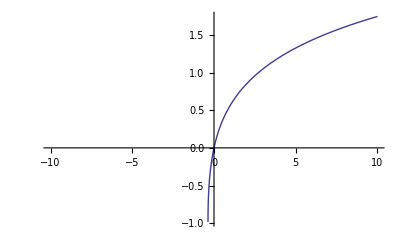

```mathematica
Plot[ProductLog[x],{x,-10,10}]
```

```mathematica
Solve[Log[x]==0,x]
```

{{x→1}}